# CBETA Chromaticity Data Analysis

## Setup

## Constants

```mathematica
MeV=10^6;
```

## Plotting Settings

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## CBETA Fieldmap Data

## Import of Data

Some problems with I/O: need to put in the \\ instead of \ and also check that the interpreter works when the fudge idata=Drop[idata,1] line is removed.

### FA/FB Data

```mathematica
idata=Import["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\i.txt","Words"];
```

```mathematica
idata=Table[Interpreter["Number"][idata⟦i⟧],{i,0,Length[idata]}];
```

```mathematica
idata=Drop[idata,1];
```

```mathematica
idata=Partition[idata,4];
```

### ZX Data

```mathematica
hdata=Import["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\h.txt","Words"];
```

```mathematica
hdata=Table[Interpreter["Number"][hdata⟦i⟧],{i,0,Length[hdata]}];
```

```mathematica
hdata=Drop[hdata,1];
```

```mathematica
hdata=Partition[hdata,3];
```

## FA/FB Arc Tune

```mathematica
arctune={idata⟦All,1⟧/MeV,ArcCos[idata⟦All,2⟧/2]/(2*π),ArcCos[idata⟦All,3⟧/2]/(2*π)};
```

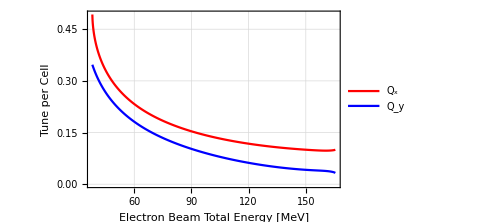

```mathematica
FAFBtuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2]},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x","Q_y"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.4}],ImageSize->Medium]
```

## FA/FB Arc Chromaticity

```mathematica
arcchrom=Table[{(arctune⟦2,i+1⟧-arctune⟦2,i⟧)/(arctune⟦1,i+1⟧-arctune⟦1,i⟧)*arctune⟦1,i+1⟧,(arctune⟦3,i+1⟧-arctune⟦3,i⟧)/(arctune⟦1,i+1⟧-arctune⟦1,i⟧)*arctune⟦1,i+1⟧},{i,1,(Length[arctune⟦1⟧]-1)}];
```

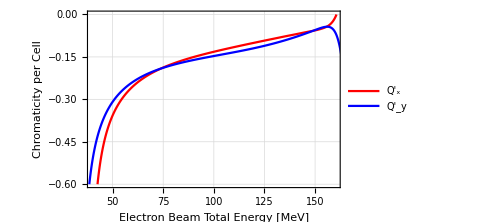

```mathematica
FAFBchromplot=ListLinePlot[{Partition[Riffle[Drop[arctune⟦1,All⟧,1],arcchrom⟦All,1⟧],2],Partition[Riffle[Drop[arctune⟦1,All⟧,1],arcchrom⟦All,2⟧],2]},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Chromaticity per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Chromaticity",*)PlotLegends->Placed[LineLegend[{"Q'_x","Q'_y"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.4}],PlotRange->{{40,160},{-0.6,0}},ImageSize->Medium]
```

## ZX Straight Tune

```mathematica
straighttune={hdata⟦All,1⟧/MeV,ArcCos[hdata⟦All,2⟧/2]/(2*π),ArcCos[hdata⟦All,3⟧/2]/(2*π)};
```

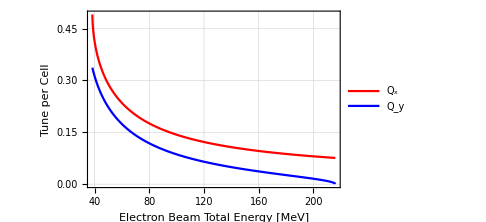

```mathematica
ZXtuneplot=ListLinePlot[{Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2],Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2]},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA ZX Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x","Q_y"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.4}],ImageSize->Medium]
```

## ZX Straight Chromaticity

```mathematica
straightchrom=Table[{(straighttune⟦2,i+1⟧-straighttune⟦2,i⟧)/(straighttune⟦1,i+1⟧-straighttune⟦1,i⟧)*straighttune⟦1,i+1⟧,(straighttune⟦3,i+1⟧-straighttune⟦3,i⟧)/(straighttune⟦1,i+1⟧-straighttune⟦1,i⟧)*straighttune⟦1,i+1⟧},{i,1,(Length[straighttune⟦1⟧]-1)}];
```

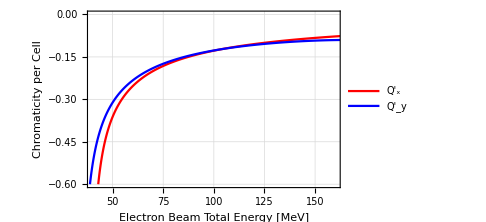

```mathematica
ZXchromplot=ListLinePlot[{Partition[Riffle[Drop[straighttune⟦1,All⟧,1],straightchrom⟦All,1⟧],2],Partition[Riffle[Drop[straighttune⟦1,All⟧,1],straightchrom⟦All,2⟧],2]},Frame->True,PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Chromaticity per Cell"},(*PlotLabel->"CBETA FFA ZX Fieldmap Chromaticity",*)PlotLegends->Placed[LineLegend[{"Q'_x","Q'_y"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.4}],PlotRange->{{40,160},{-0.6,0}},ImageSize->Medium]
```

## Combined Fieldmap Plots

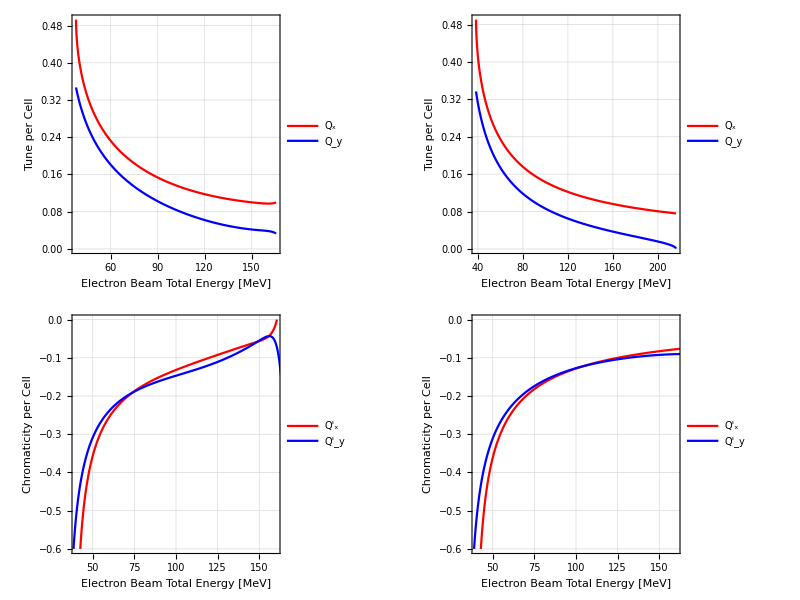

```mathematica
fieldmap=Grid[{{FAFBtuneplot,ZXtuneplot},{FAFBchromplot,ZXchromplot}}]
```

## Saving of Fieldmap Plots

```mathematica
SetDirectory["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\Fieldmap_Plots"];
Export["FAFB_fieldmap_tune.pdf",FAFBtuneplot];
Export["ZX_fieldmap_tune.pdf",ZXtuneplot];
Export["FAFB_fieldmap_chrom.pdf",FAFBchromplot];
Export["ZX_fieldmap_chrom.pdf",ZXchromplot];
Export["fieldmap_grid.pdf",fieldmap];
```

## Nominal Tune Data Analysis

## Data Import

### Tune Data

Tune data is of the form of 12 consecutive blocks of 4 x 30. The 12 blocks are {All, FA, TA, ZX, TB, FB} × {x, y}.

```mathematica
tunedata=Import["C:\\Users\\user\\Documents\\Wolfram Mathematica\\CBETAchromaticity\\Chromaticity_Data\\tune_vals.csv","csv"];
```

## Intermediaries + Energy

```mathematica
Nominalenergies={42,78,114,150};
```

Measured Energies are in the order 150 → 149.25 MeV, 114 → 113.43 MeV etc. Each energy only gets a maximum -0.5% kick. Assumed this is the case for now!

```mathematica
Measuredenergies=Reverse[Table[(1+ΔEe)*Nominalenergies⟦j⟧,{j,1,4},{ΔEe,0,-0.005,-0.005/(Length[tunedata⟦All,1⟧]-1)}],2];
```

## Measured Nominal Tunes

### FA Nominal Tunes

```mathematica
FAmeasuredNOMx=Partition[Riffle[Nominalenergies,tunedata⟦-1,9;;12⟧],2];
```

```mathematica
FAmeasuredNOMy=Partition[Riffle[Nominalenergies,tunedata⟦-1,13;;16⟧],2];
```

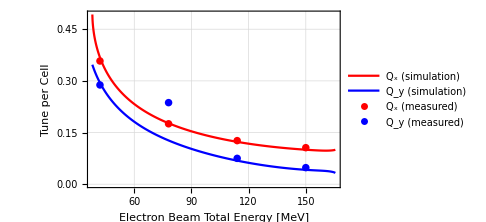

```mathematica
FAtuneNOMplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FAmeasuredNOMx,FAmeasuredNOMy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.7}],ImageSize->Medium]
```

### FB Nominal Tunes

```mathematica
FBmeasuredNOMx=Partition[Riffle[Nominalenergies,tunedata⟦-1,41;;44⟧],2];
```

```mathematica
FBmeasuredNOMy=Partition[Riffle[Nominalenergies,tunedata⟦-1,45;;48⟧],2];
```

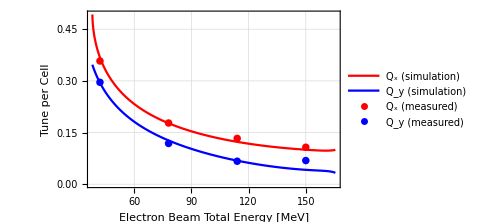

```mathematica
FBtuneNOMplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FBmeasuredNOMx,FBmeasuredNOMy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.7}],ImageSize->Medium]
```

### ZX Nominal Tunes

```mathematica
ZXmeasuredNOMx=Partition[Riffle[Nominalenergies,tunedata⟦-1,25;;28⟧],2];
```

```mathematica
ZXmeasuredNOMy=Partition[Riffle[Nominalenergies,tunedata⟦-1,29;;32⟧],2];
```

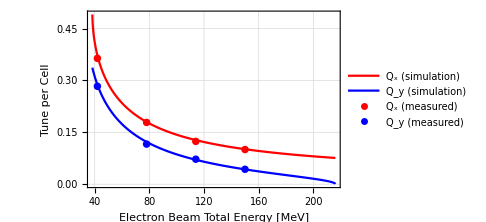

```mathematica
ZXtuneNOMplot=ListPlot[{Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2],Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2],ZXmeasuredNOMx,ZXmeasuredNOMy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA ZX Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.7}],ImageSize->Medium]
```

```mathematica
NOMtunegrid=Grid[{{FAtuneNOMplot,FBtuneNOMplot},{ZXtuneNOMplot}}]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
SetDirectory["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\Tune_Plots"];
Export["FAFBZX_nominal_tunes.pdf",NOMtunegrid];
```

## Chromaticity Tune Data

## FA

### FA 42 MeV Measured Data

```mathematica
FA42measuredx=Partition[Riffle[Measuredenergies⟦1⟧,tunedata⟦All,9⟧],2];
```

```mathematica
FA42measuredy=Partition[Riffle[Measuredenergies⟦1⟧,tunedata⟦All,13⟧],2];
```

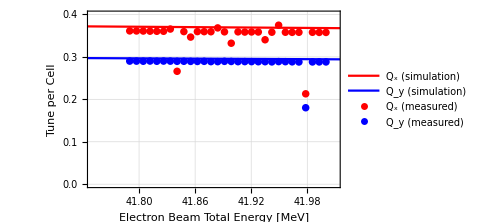

```mathematica
FA42tuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FA42measuredx,FA42measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.3}],PlotRange->{{41.75,42.01},{0,0.4}},ImageSize->Medium]
```

### FA 42 MeV ν_x Tune

```mathematica
FA42xgooddat=Delete[FA42measuredx,Partition[DeleteCases[Table[If[Abs[FA42measuredx⟦i,2⟧-Mean[FA42measuredx⟦All,2⟧]]>2*StandardDeviation[FA42measuredx⟦All,2⟧],i],{i,1,Length[FA42measuredx]}],Null],1]];
```

```mathematica
FA42xpart1drop=Fit[FA42xgooddat,{1,x},x]⟦1⟧
```

1.00685

```mathematica
FA42xpart2drop=Fit[FA42xgooddat,{1,x},x]⟦2,1⟧
```

-0.015481

```mathematica
FA42xdroppedpoints=FA42measuredx⟦DeleteCases[Table[If[Abs[FA42measuredx⟦i,2⟧-Mean[FA42measuredx⟦All,2⟧]]>2*StandardDeviation[FA42measuredx⟦All,2⟧],i],{i,1,Length[FA42measuredx]}],Null]⟧
```

{{41.8407,0.26612},{41.9783,0.21306}}

```mathematica
FA42xbestfitpoints=Table[{x,FA42xpart1drop+FA42xpart2drop*x},{x,Min[FA42measuredx⟦All,1⟧],Max[FA42measuredx⟦All,1⟧],0.01}];
```

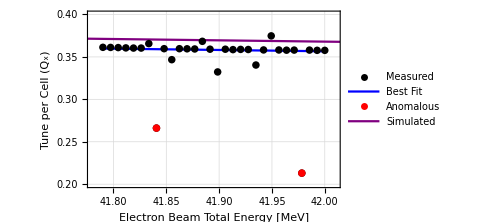

```mathematica
FA42xtune=ListPlot[{FA42measuredx,FA42xbestfitpoints,FA42xdroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.35}],PlotRange->{{41.78,42.01},{0.2,0.4}},ImageSize->Medium]
```

### FA 42 MeV ξ_x Chromaticity

```mathematica
FA42xΔEeEeΔQ=Table[{(FA42xgooddat⟦-1,1⟧-FA42xgooddat⟦i,1⟧)/FA42xgooddat⟦-1,1⟧,FA42xgooddat⟦-1,2⟧-FA42xgooddat⟦i,2⟧},{i,1,(Length[FA42xgooddat⟦All,1⟧]-1)}];
```

```mathematica
FA42xΔEeEeΔQgooddat=Delete[FA42xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FA42xΔEeEeΔQ⟦i,2⟧-Mean[FA42xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA42xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA42xΔEeEeΔQ]}],Null],1]];
```

```mathematica
FA42xpart1chromgood=Fit[FA42xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.000119933

```mathematica
FA42xpart2chromgood=Fit[FA42xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.669418

```mathematica
FA42xΔEeEeΔQbestfitpoints=Table[{x,FA42xpart1chromgood+FA42xpart2chromgood*x},{x,Min[FA42xΔEeEeΔQ⟦All,1⟧],Max[FA42xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FA42xΔEeEeΔQdroppedpoints=FA42xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FA42xΔEeEeΔQ⟦i,2⟧-Mean[FA42xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA42xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA42xΔEeEeΔQ]}],Null]⟧;
```

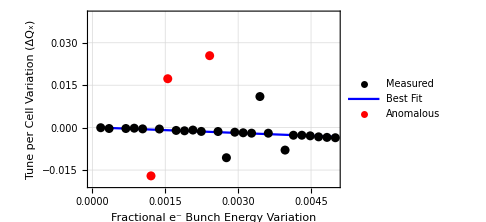

```mathematica
FA42xchromplot=ListPlot[{FA42xΔEeEeΔQgooddat,FA42xΔEeEeΔQbestfitpoints,FA42xΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.78}],PlotRange->{{0,0.005},{-0.02,0.04}},ImageSize->Medium]
```

### FA 42 MeV ⋁_y Tune

```mathematica
FA42ygooddat=Delete[FA42measuredy,Partition[DeleteCases[Table[If[Abs[FA42measuredy⟦i,2⟧-Mean[FA42measuredy⟦All,2⟧]]>2*StandardDeviation[FA42measuredy⟦All,2⟧],i],{i,1,Length[FA42measuredy]}],Null],1]];
```

```mathematica
FA42ypart1drop=Fit[FA42ygooddat,{1,x},x]⟦1⟧
```

0.712739

```mathematica
FA42ypart2drop=Fit[FA42ygooddat,{1,x},x]⟦2,1⟧
```

-0.0101115

```mathematica
FA42ydroppedpoints=FA42measuredy⟦DeleteCases[Table[If[Abs[FA42measuredy⟦i,2⟧-Mean[FA42measuredy⟦All,2⟧]]>2*StandardDeviation[FA42measuredy⟦All,2⟧],i],{i,1,Length[FA42measuredy]}],Null]⟧
```

{{41.9783,0.18023}}

```mathematica
FA42ybestfitpoints=Table[{x,FA42ypart1drop+FA42ypart2drop*x},{x,Min[FA42measuredy⟦All,1⟧],Max[FA42measuredy⟦All,1⟧],0.01}];
```

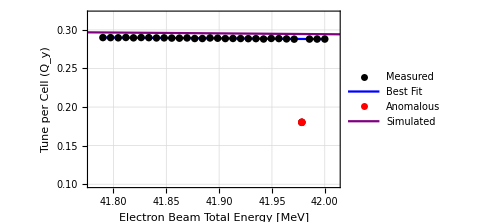

```mathematica
FA42ytune=ListPlot[{FA42measuredy,FA42ybestfitpoints,FA42ydroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.35}],PlotRange->{{41.78,42.01},{0.1,0.32}},ImageSize->Medium]
```

### FA 42 MeV ξ_y Chromaticity

```mathematica
FA42yΔEeEeΔQ=Table[{(FA42ygooddat⟦-1,1⟧-FA42ygooddat⟦i,1⟧)/FA42ygooddat⟦-1,1⟧,FA42ygooddat⟦-1,2⟧-FA42ygooddat⟦i,2⟧},{i,1,(Length[FA42ygooddat⟦All,1⟧]-1)}];
```

```mathematica
FA42yΔEeEeΔQgooddat=Delete[FA42yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FA42yΔEeEeΔQ⟦i,2⟧-Mean[FA42yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA42yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA42yΔEeEeΔQ]}],Null],1]];
```

```mathematica
FA42ypart1chromgood=Fit[FA42yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.000110281

```mathematica
FA42ypart2chromgood=Fit[FA42yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.429198

```mathematica
FA42yΔEeEeΔQbestfitpoints=Table[{x,FA42ypart1chromgood+FA42ypart2chromgood*x},{x,Min[FA42yΔEeEeΔQ⟦All,1⟧],Max[FA42yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FA42yΔEeEeΔQdroppedpoints=FA42yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FA42yΔEeEeΔQ⟦i,2⟧-Mean[FA42yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA42yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA42yΔEeEeΔQ]}],Null]⟧;
```

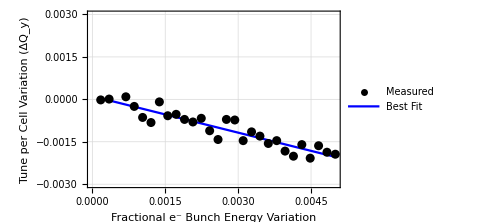

```mathematica
FA42ychromplot=ListPlot[{FA42yΔEeEeΔQgooddat,FA42yΔEeEeΔQbestfitpoints(*,FA42yΔEeEeΔQdroppedpoints*)},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.78}],PlotRange->{{0,0.005},{-0.003,0.003}},ImageSize->Medium]
```

### FA 78 MeV Measured Data

```mathematica
FA78measuredx=Partition[Riffle[Measuredenergies⟦2⟧,tunedata⟦All,10⟧],2];
```

```mathematica
FA78measuredy=Partition[Riffle[Measuredenergies⟦2⟧,tunedata⟦All,14⟧],2];
```

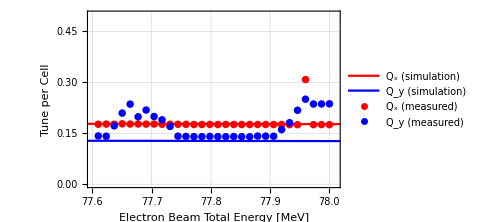

```mathematica
FA78tuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FA78measuredx,FA78measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.7}],PlotRange->{{77.6,78.01},{0,0.5}},ImageSize->Medium]
```

### FA 78 MeV ν_x Tune

```mathematica
FA78xgooddat=Delete[FA78measuredx,Partition[DeleteCases[Table[If[Abs[FA78measuredx⟦i,2⟧-Mean[FA78measuredx⟦All,2⟧]]>2*StandardDeviation[FA78measuredx⟦All,2⟧],i],{i,1,Length[FA78measuredx]}],Null],1]];
```

```mathematica
FA78xpart1drop=Fit[FA78xgooddat,{1,x},x]⟦1⟧
```

0.580938

```mathematica
FA78xpart2drop=Fit[FA78xgooddat,{1,x},x]⟦2,1⟧
```

-0.00520205

```mathematica
FA78xdroppedpoints=FA78measuredx⟦DeleteCases[Table[If[Abs[FA78measuredx⟦i,2⟧-Mean[FA78measuredx⟦All,2⟧]]>2*StandardDeviation[FA78measuredx⟦All,2⟧],i],{i,1,Length[FA78measuredx]}],Null]⟧
```

{{77.9597,0.30828}}

```mathematica
FA78xbestfitpoints=Table[{x,FA78xpart1drop+FA78xpart2drop*x},{x,Min[FA78measuredx⟦All,1⟧],Max[FA78measuredx⟦All,1⟧],0.01}];
```

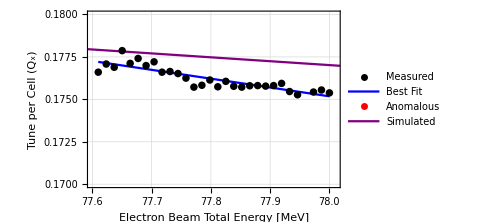

```mathematica
FA78xtune=ListPlot[{FA78measuredx,FA78xbestfitpoints,FA78xdroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.3}],PlotRange->{{77.6,78.01},{0.17,0.18}},ImageSize->Medium]
```

Note that the anomalous point is beyond the range of this plot.

### FA 78 MeV ξ_x Chromaticity

```mathematica
FA78xΔEeEeΔQ=Table[{(FA78xgooddat⟦-1,1⟧-FA78xgooddat⟦i,1⟧)/FA78xgooddat⟦-1,1⟧,FA78xgooddat⟦-1,2⟧-FA78xgooddat⟦i,2⟧},{i,1,(Length[FA78xgooddat⟦All,1⟧]-1)}];
```

```mathematica
FA78xΔEeEeΔQgooddat=Delete[FA78xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FA78xΔEeEeΔQ⟦i,2⟧-Mean[FA78xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA78xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA78xΔEeEeΔQ]}],Null],1]];
```

```mathematica
FA78xpart1chromgood=Fit[FA78xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.000185926

```mathematica
FA78xpart2chromgood=Fit[FA78xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.384286

```mathematica
FA78xΔEeEeΔQbestfitpoints=Table[{x,FA78xpart1chromgood+FA78xpart2chromgood*x},{x,Min[FA78xΔEeEeΔQ⟦All,1⟧],Max[FA78xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FA78xΔEeEeΔQdroppedpoints=FA78xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FA78xΔEeEeΔQ⟦i,2⟧-Mean[FA78xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA78xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA78xΔEeEeΔQ]}],Null]⟧;
```

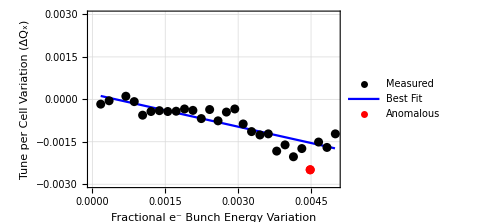

```mathematica
FA78xchromplot=ListPlot[{FA78xΔEeEeΔQgooddat,FA78xΔEeEeΔQbestfitpoints,FA78xΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.75}],PlotRange->{{0,0.005},{-0.003,0.003}},ImageSize->Medium]
```

### FA 78 MeV ν_y Tune

```mathematica
FA78ygooddat=Delete[FA78measuredy,Partition[DeleteCases[Table[If[Abs[FA78measuredy⟦i,2⟧-Mean[FA78measuredy⟦All,2⟧]]>2*StandardDeviation[FA78measuredy⟦All,2⟧],i],{i,1,Length[FA78measuredy]}],Null],1]];
```

```mathematica
FA78ypart1drop=Fit[FA78ygooddat,{1,x},x]⟦1⟧
```

-5.4188

```mathematica
FA78ypart2drop=Fit[FA78ygooddat,{1,x},x]⟦2,1⟧
```

0.0718842

```mathematica
FA78ydroppedpoints=FA78measuredy⟦DeleteCases[Table[If[Abs[FA78measuredy⟦i,2⟧-Mean[FA78measuredy⟦All,2⟧]]>2*StandardDeviation[FA78measuredy⟦All,2⟧],i],{i,1,Length[FA78measuredy]}],Null]⟧
```

{}

```mathematica
FA78ybestfitpoints=Table[{x,FA78ypart1drop+FA78ypart2drop*x},{x,Min[FA78measuredy⟦All,1⟧],Max[FA78measuredy⟦All,1⟧],0.01}];
```

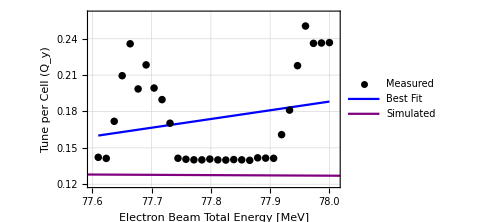

```mathematica
FA78ytune=ListPlot[{FA78measuredy,FA78ybestfitpoints,(*FA78ydroppedpoints,*)Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2]},Joined->{False,True,(*False,*)True},PlotStyle->{{Black,PointSize[0.015]},Blue,(*{Red,PointSize[0.015]},*)Purple},Frame->True,PlotStyle->{Red,Blue,(*{Red,PointSize[0.015]},*){Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit",(*"Anomalous",*)"Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.55,0.75}],PlotRange->{{77.6,78.01},{0.12,0.26}},ImageSize->Medium]
```

### FA 78 MeV ξ_y Chromaticity

```mathematica
FA78yΔEeEeΔQ=Table[{(FA78ygooddat⟦-1,1⟧-FA78ygooddat⟦i,1⟧)/FA78ygooddat⟦-1,1⟧,FA78ygooddat⟦-1,2⟧-FA78ygooddat⟦i,2⟧},{i,1,(Length[FA78ygooddat⟦All,1⟧]-1)}];
```

```mathematica
FA78yΔEeEeΔQgooddat=Delete[FA78yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FA78yΔEeEeΔQ⟦i,2⟧-Mean[FA78yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA78yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA78yΔEeEeΔQ]}],Null],1]];
```

```mathematica
FA78ypart1chromgood=Fit[FA78yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.0655161

```mathematica
FA78ypart2chromgood=Fit[FA78yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

0.793181

```mathematica
FA78yΔEeEeΔQbestfitpoints=Table[{x,FA78ypart1chromgood+FA78ypart2chromgood*x},{x,Min[FA78yΔEeEeΔQ⟦All,1⟧],Max[FA78yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FA78yΔEeEeΔQdroppedpoints=FA78yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FA78yΔEeEeΔQ⟦i,2⟧-Mean[FA78yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA78yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA78yΔEeEeΔQ]}],Null]⟧
```

{{0.000517241,-0.01367}}

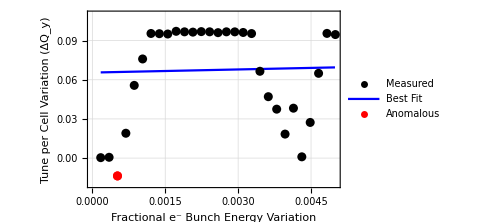

```mathematica
FA78ychromplot=ListPlot[{FA78yΔEeEeΔQgooddat,FA78yΔEeEeΔQbestfitpoints,FA78yΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.45,0.4}],PlotRange->{{0,0.005},{-0.02,0.11}},ImageSize->Medium]
```

### FA 114 MeV Measured Data

```mathematica
FA114measuredx=Partition[Riffle[Measuredenergies⟦3⟧,tunedata⟦All,11⟧],2];
```

```mathematica
FA114measuredy=Partition[Riffle[Measuredenergies⟦3⟧,tunedata⟦All,15⟧],2];
```

```mathematica
FA114tuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FA114measuredx,FA114measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{113.4,114.01},{0,0.35}},ImageSize->Medium];
```

### FA 114 MeV ν_x Tune

```mathematica
FA114xgooddat=Delete[FA114measuredx,Partition[DeleteCases[Table[If[Abs[FA114measuredx⟦i,2⟧-Mean[FA114measuredx⟦All,2⟧]]>2*StandardDeviation[FA114measuredx⟦All,2⟧],i],{i,1,Length[FA114measuredx]}],Null],1]];
```

```mathematica
FA114xpart1drop=Fit[FA114xgooddat,{1,x},x]⟦1⟧
```

0.208887

```mathematica
FA114xpart2drop=Fit[FA114xgooddat,{1,x},x]⟦2,1⟧
```

-0.000706944

```mathematica
FA114xdroppedpoints=FA114measuredx⟦DeleteCases[Table[If[Abs[FA114measuredx⟦i,2⟧-Mean[FA114measuredx⟦All,2⟧]]>2*StandardDeviation[FA114measuredx⟦All,2⟧],i],{i,1,Length[FA114measuredx]}],Null]⟧
```

{{113.941,0.31249}}

```mathematica
FA114xbestfitpoints=Table[{x,FA114xpart1drop+FA114xpart2drop*x},{x,Min[FA114measuredx⟦All,1⟧],Max[FA114measuredx⟦All,1⟧],0.01}];
```

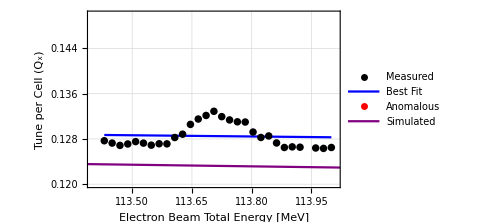

```mathematica
FA114xtune=ListPlot[{FA114measuredx,FA114xbestfitpoints,FA114xdroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],PlotRange->{{113.4,114.01},{0.12,0.15}},ImageSize->Medium]
```

Note that the anomalous point is beyond the range of this plot.

### FA 14 MeV ξ_x Chromaticity

```mathematica
FA114xΔEeEeΔQ=Table[{(FA114xgooddat⟦-1,1⟧-FA114xgooddat⟦i,1⟧)/FA114xgooddat⟦-1,1⟧,FA114xgooddat⟦-1,2⟧-FA114xgooddat⟦i,2⟧},{i,1,(Length[FA114xgooddat⟦All,1⟧]-1)}];
```

```mathematica
FA114xΔEeEeΔQgooddat=Delete[FA114xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FA114xΔEeEeΔQ⟦i,2⟧-Mean[FA114xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA114xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA114xΔEeEeΔQ]}],Null],1]];
```

```mathematica
FA114xpart1chromgood=Fit[FA114xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

-0.00192324

```mathematica
FA114xpart2chromgood=Fit[FA114xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.000592816

```mathematica
FA114xΔEeEeΔQbestfitpoints=Table[{x,FA114xpart1chromgood+FA114xpart2chromgood*x},{x,Min[FA114xΔEeEeΔQ⟦All,1⟧],Max[FA114xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FA114xΔEeEeΔQdroppedpoints=FA114xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FA114xΔEeEeΔQ⟦i,2⟧-Mean[FA114xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA114xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA114xΔEeEeΔQ]}],Null]⟧;
```

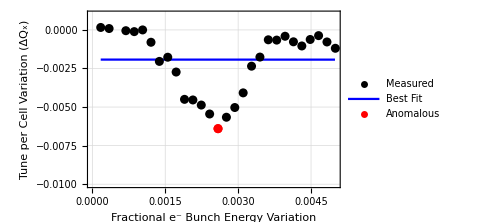

```mathematica
FA114xchromplot=ListPlot[{FA114xΔEeEeΔQgooddat,FA114xΔEeEeΔQbestfitpoints,FA114xΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.25}],PlotRange->{{0,0.005},{-0.01,0.001}},ImageSize->Medium]
```

### FA 114 MeV ν_y Tune

```mathematica
FA114ygooddat=Delete[FA114measuredy,Partition[DeleteCases[Table[If[Abs[FA114measuredy⟦i,2⟧-Mean[FA114measuredy⟦All,2⟧]]>2*StandardDeviation[FA114measuredy⟦All,2⟧],i],{i,1,Length[FA114measuredy]}],Null],1]];
```

```mathematica
FA114ypart1drop=Fit[FA114ygooddat,{1,x},x]⟦1⟧
```

0.0830528

```mathematica
FA114ypart2drop=Fit[FA114ygooddat,{1,x},x]⟦2,1⟧
```

-0.0000710086

```mathematica
FA114ydroppedpoints=FA114measuredy⟦DeleteCases[Table[If[Abs[FA114measuredy⟦i,2⟧-Mean[FA114measuredy⟦All,2⟧]]>2*StandardDeviation[FA114measuredy⟦All,2⟧],i],{i,1,Length[FA114measuredy]}],Null]⟧
```

{{113.941,0.12834}}

```mathematica
FA114ybestfitpoints=Table[{x,FA114ypart1drop+FA114ypart2drop*x},{x,Min[FA114measuredy⟦All,1⟧],Max[FA114measuredy⟦All,1⟧],0.01}];
```

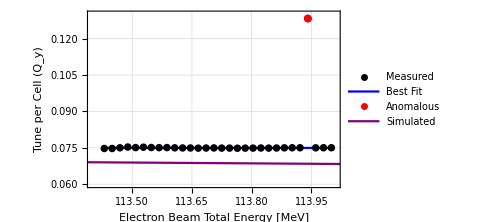

```mathematica
FA114ytune=ListPlot[{FA114measuredy,FA114ybestfitpoints,FA114ydroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{113.4,114.01},{0.06,0.13}},ImageSize->Medium]
```

### FA 114 MeV ξ_y Chromaticity

```mathematica
FA114yΔEeEeΔQ=Table[{(FA114ygooddat⟦-1,1⟧-FA114ygooddat⟦i,1⟧)/FA114ygooddat⟦-1,1⟧,FA114ygooddat⟦-1,2⟧-FA114ygooddat⟦i,2⟧},{i,1,(Length[FA114ygooddat⟦All,1⟧]-1)}];
```

```mathematica
FA114yΔEeEeΔQgooddat=Delete[FA114yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FA114yΔEeEeΔQ⟦i,2⟧-Mean[FA114yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA114yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA114yΔEeEeΔQ]}],Null],1]];
```

```mathematica
FA114ypart1chromgood=Fit[FA114yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.0000640961

```mathematica
FA114ypart2chromgood=Fit[FA114yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

0.00946679

```mathematica
FA114yΔEeEeΔQbestfitpoints=Table[{x,FA114ypart1chromgood+FA114ypart2chromgood*x},{x,Min[FA114yΔEeEeΔQ⟦All,1⟧],Max[FA114yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FA114yΔEeEeΔQdroppedpoints=FA114yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FA114yΔEeEeΔQ⟦i,2⟧-Mean[FA114yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FA114yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FA114yΔEeEeΔQ]}],Null]⟧
```

{{0.00448276,-0.00029},{0.00413793,-0.00022}}

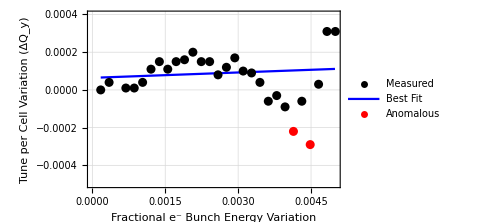

```mathematica
FA114ychromplot=ListPlot[{FA114yΔEeEeΔQgooddat,FA114yΔEeEeΔQbestfitpoints,FA114yΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.25}],PlotRange->{{0,0.005},{-0.0005,0.0004}},ImageSize->Medium]
```

### FA 150 MeV Measured Data

```mathematica
FA150measuredx=Partition[Riffle[Measuredenergies⟦4⟧,tunedata⟦All,12⟧],2];
```

```mathematica
FA150measuredy=Partition[Riffle[Measuredenergies⟦4⟧,tunedata⟦All,16⟧],2];
```

```mathematica
FA150tuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FA150measuredx,FA150measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.6}],PlotRange->{{148,150.01},{0,0.4}},ImageSize->Medium];
```

Obviously with the poor quality data in the 4th turn, we can’t provide an accurate chromaticity measurement. Therefore, this is neglected.

### FA Group Plots

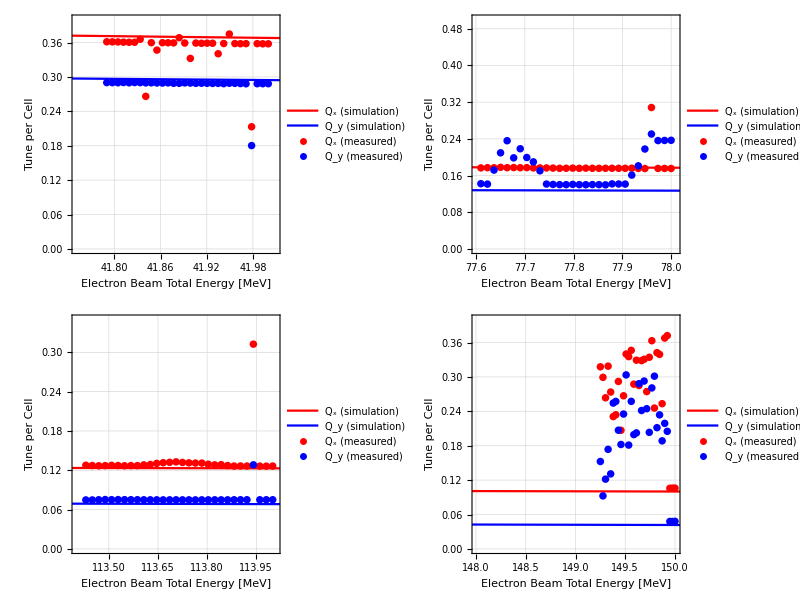

```mathematica
FAtunegrid=Grid[{{FA42tuneplot,FA78tuneplot},{FA114tuneplot,FA150tuneplot}}]
```

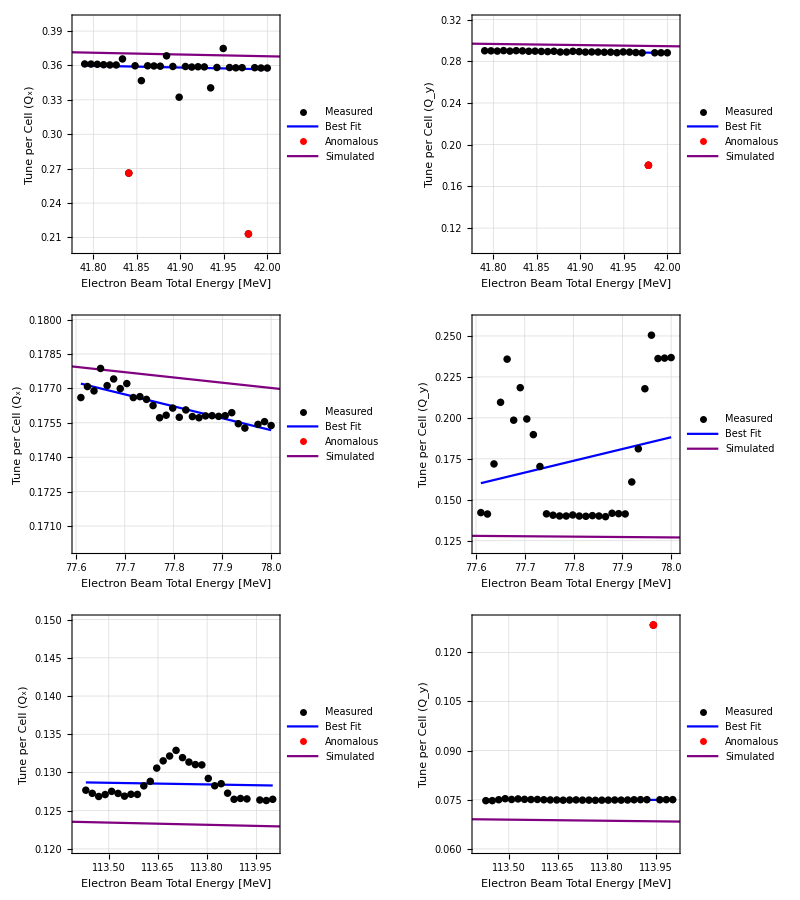

```mathematica
FAtuneanalysedgrid=Grid[{{FA42xtune,FA42ytune},{FA78xtune,FA78ytune},{FA114xtune,FA114ytune}}]
```

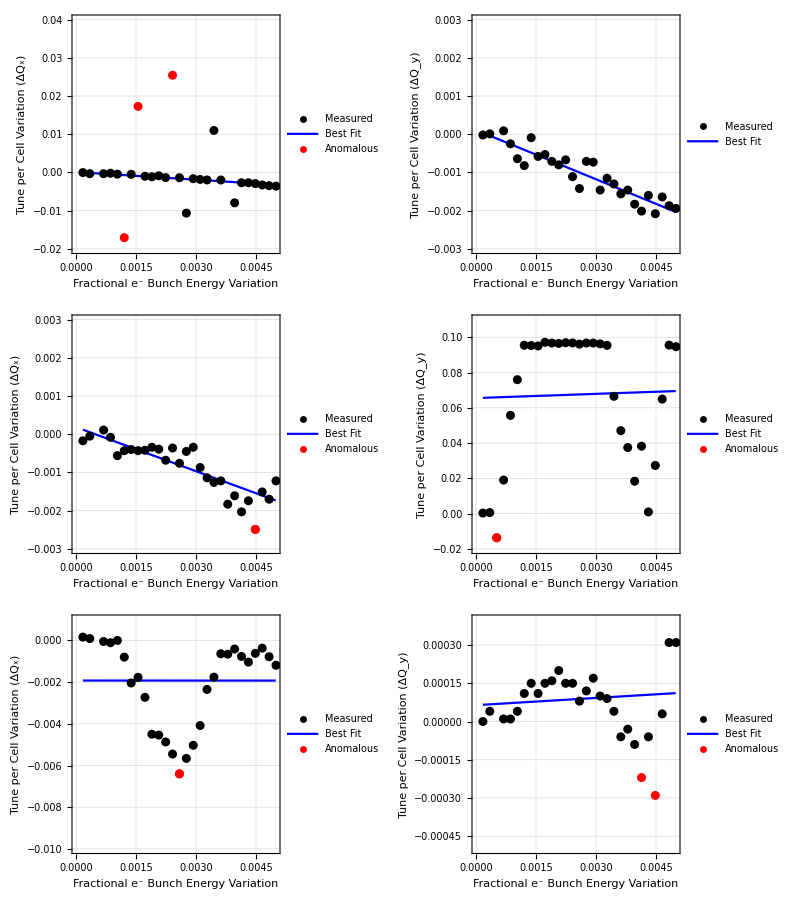

```mathematica
FAchromanalysedgrid=Grid[{{FA42xchromplot,FA42ychromplot},{FA78xchromplot,FA78ychromplot},{FA114xchromplot,FA114ychromplot}}]
```

```mathematica
FAchromtable=Grid[{{"Electron Beam Total Energy [MeV]","FA ξ_x (measured)","FA ξ_y (measured)"},{"42",FA42xpart2chromgood,FA42ypart2chromgood},{"78",FA78xpart2chromgood,FA78ypart2chromgood},{"114",FA114xpart2chromgood,FA114ypart2chromgood}},Dividers->All]
```

Electron Beam Total Energy [MeV] | FA ξ_x (measured) | FA ξ_y (measured)
42 | -0.669418 | -0.429198
78 | -0.384286 | 0.793181
114 | -0.000592816 | 0.00946679

```mathematica
FAchromvals={Nominalenergies⟦1;;3⟧,{FA42xpart2chromgood,FA78xpart2chromgood,FA114xpart2chromgood},{FA42ypart2chromgood,FA78ypart2chromgood,FA114ypart2chromgood}};
```

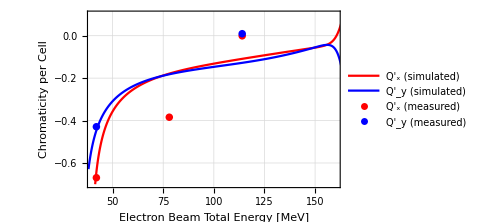

```mathematica
FAchrommeasured=ListPlot[{Partition[Riffle[Drop[arctune⟦1,All⟧,1],arcchrom⟦All,1⟧],2],Partition[Riffle[Drop[arctune⟦1,All⟧,1],arcchrom⟦All,2⟧],2],Partition[Riffle[FAchromvals⟦1,All⟧,FAchromvals⟦2,All⟧],2],Partition[Riffle[FAchromvals⟦1,All⟧,FAchromvals⟦3,All⟧],2]},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Chromaticity per Cell"},PlotLegends->Placed[LineLegend[{"Q'_x (simulated)","Q'_y (simulated)","Q'_x (measured)","Q'_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.3}],PlotRange->{{40,160},{-0.7,0.1}},ImageSize->Medium]
```

Why are my results so shit?

```mathematica
SetDirectory["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\Tune_Plots"];
Export["FA_analysed_3turn_tunes.pdf",FAtuneanalysedgrid];
Export["FA_analysed_3turn_dEedQ.pdf",FAchromanalysedgrid];
Export["FA_analysed_chromaticity.pdf",FAchrommeasured];
```

## FB

### FB 42 MeV Measured Data

```mathematica
FB42measuredx=Partition[Riffle[Measuredenergies⟦1⟧,tunedata⟦All,41⟧],2];
```

```mathematica
FB42measuredy=Partition[Riffle[Measuredenergies⟦1⟧,tunedata⟦All,45⟧],2];
```

```mathematica
FB42tuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FB42measuredx,FB42measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.3}],PlotRange->{{41.75,42.01},{0,0.4}},ImageSize->Medium];
```

### FB 42 MeV ν_x Tune

```mathematica
FB42xgooddat=Delete[FB42measuredx,Partition[DeleteCases[Table[If[Abs[FB42measuredx⟦i,2⟧-Mean[FB42measuredx⟦All,2⟧]]>2*StandardDeviation[FB42measuredx⟦All,2⟧],i],{i,1,Length[FB42measuredx]}],Null],1]];
```

```mathematica
FB42xpart1drop=Fit[FB42xgooddat,{1,x},x]⟦1⟧
```

3.77445

```mathematica
FB42xpart2drop=Fit[FB42xgooddat,{1,x},x]⟦2,1⟧
```

-0.0817169

```mathematica
FB42xdroppedpoints=FB42measuredx⟦DeleteCases[Table[If[Abs[FB42measuredx⟦i,2⟧-Mean[FB42measuredx⟦All,2⟧]]>2*StandardDeviation[FB42measuredx⟦All,2⟧],i],{i,1,Length[FB42measuredx]}],Null]⟧
```

{{41.8407,0.24296},{41.8841,0.17035},{41.9783,0.22627}}

```mathematica
FB42xbestfitpoints=Table[{x,FB42xpart1drop+FB42xpart2drop*x},{x,Min[FB42measuredx⟦All,1⟧],Max[FB42measuredx⟦All,1⟧],0.01}];
```

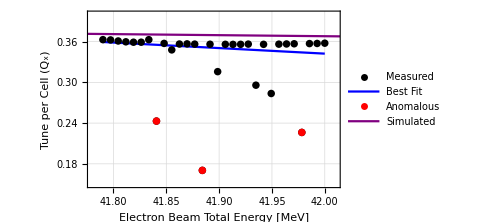

```mathematica
FB42xtune=ListPlot[{FB42measuredx,FB42xbestfitpoints,FB42xdroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.37}],PlotRange->{{41.78,42.01},{0.15,0.4}},ImageSize->Medium]
```

### FB 42 MeV ξ_x Chromaticity

```mathematica
FB42xΔEeEeΔQ=Table[{(FB42xgooddat⟦-1,1⟧-FB42xgooddat⟦i,1⟧)/FB42xgooddat⟦-1,1⟧,FB42xgooddat⟦-1,2⟧-FB42xgooddat⟦i,2⟧},{i,1,(Length[FB42xgooddat⟦All,1⟧]-1)}];
```

```mathematica
FB42xΔEeEeΔQgooddat=Delete[FB42xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FB42xΔEeEeΔQ⟦i,2⟧-Mean[FB42xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB42xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB42xΔEeEeΔQ]}],Null],1]];
```

```mathematica
FB42xpart1chromgood=Fit[FB42xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.00524622

```mathematica
FB42xpart2chromgood=Fit[FB42xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-1.21876

```mathematica
FB42xΔEeEeΔQbestfitpoints=Table[{x,FB42xpart1chromgood+FB42xpart2chromgood*x},{x,Min[FB42xΔEeEeΔQ⟦All,1⟧],Max[FB42xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FB42xΔEeEeΔQdroppedpoints=FB42xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FB42xΔEeEeΔQ⟦i,2⟧-Mean[FB42xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB42xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB42xΔEeEeΔQ]}],Null]⟧
```

{{0.00155172,0.06187},{0.0012069,0.07412}}

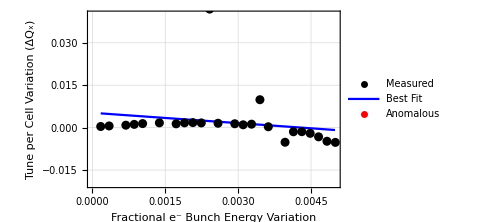

```mathematica
FB42xchromplot=ListPlot[{FB42xΔEeEeΔQgooddat,FB42xΔEeEeΔQbestfitpoints,FB42xΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.78}],PlotRange->{{0,0.005},{-0.02,0.04}},ImageSize->Medium]
```

### FB 42 MeV ν_y Tune

```mathematica
FB42ygooddat=Delete[FB42measuredy,Partition[DeleteCases[Table[If[Abs[FB42measuredy⟦i,2⟧-Mean[FB42measuredy⟦All,2⟧]]>2*StandardDeviation[FB42measuredy⟦All,2⟧],i],{i,1,Length[FB42measuredy]}],Null],1]];
```

```mathematica
FB42ypart1drop=Fit[FB42ygooddat,{1,x},x]⟦1⟧
```

-0.853314

```mathematica
FB42ypart2drop=Fit[FB42ygooddat,{1,x},x]⟦2,1⟧
```

0.0273825

```mathematica
FB42ydroppedpoints=FB42measuredy⟦DeleteCases[Table[If[Abs[FB42measuredy⟦i,2⟧-Mean[FB42measuredy⟦All,2⟧]]>2*StandardDeviation[FB42measuredy⟦All,2⟧],i],{i,1,Length[FB42measuredy]}],Null]⟧
```

{{41.9783,0.33653}}

```mathematica
FB42ybestfitpoints=Table[{x,FB42ypart1drop+FB42ypart2drop*x},{x,Min[FB42measuredy⟦All,1⟧],Max[FB42measuredy⟦All,1⟧],0.01}];
```

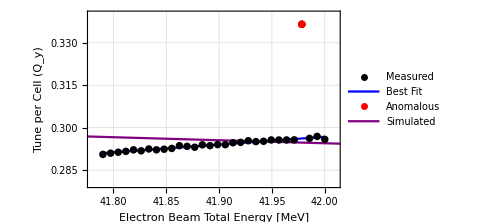

```mathematica
FB42ytune=ListPlot[{FB42measuredy,FB42ybestfitpoints,FB42ydroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],PlotRange->{{41.78,42.01},{0.28,0.34}},ImageSize->Medium]
```

### FB 42 MeV ξ_y Chromaticity

```mathematica
FB42yΔEeEeΔQ=Table[{(FB42ygooddat⟦-1,1⟧-FB42ygooddat⟦i,1⟧)/FB42ygooddat⟦-1,1⟧,FB42ygooddat⟦-1,2⟧-FB42ygooddat⟦i,2⟧},{i,1,(Length[FB42ygooddat⟦All,1⟧]-1)}];
```

```mathematica
FB42yΔEeEeΔQgooddat=Delete[FB42yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FB42yΔEeEeΔQ⟦i,2⟧-Mean[FB42yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB42yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB42yΔEeEeΔQ]}],Null],1]];
```

```mathematica
FB42ypart1chromgood=Fit[FB42yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

-0.00104926

```mathematica
FB42ypart2chromgood=Fit[FB42yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

1.19302

```mathematica
FB42yΔEeEeΔQbestfitpoints=Table[{x,FB42ypart1chromgood+FB42ypart2chromgood*x},{x,Min[FB42yΔEeEeΔQ⟦All,1⟧],Max[FB42yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FB42yΔEeEeΔQdroppedpoints=FB42yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FB42yΔEeEeΔQ⟦i,2⟧-Mean[FB42yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB42yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB42yΔEeEeΔQ]}],Null]⟧
```

{}

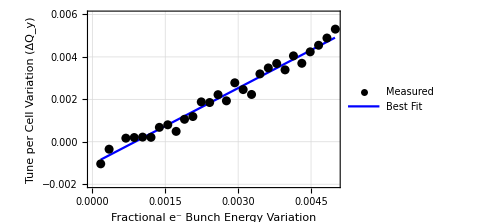

```mathematica
FB42ychromplot=ListPlot[{FB42yΔEeEeΔQgooddat,FB42yΔEeEeΔQbestfitpoints(*,FB42yΔEeEeΔQdroppedpoints*)},Joined->{False,True(*,False*)},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue(*,{Red,PointSize[0.018]}*)},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit"(*,"Anomalous"*)},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.78}],PlotRange->{{0,0.005},{-0.002,0.006}},ImageSize->Medium]
```

### FB 78 MeV Measured Data

```mathematica
FB78measuredx=Partition[Riffle[Measuredenergies⟦2⟧,tunedata⟦All,42⟧],2];
```

```mathematica
FB78measuredy=Partition[Riffle[Measuredenergies⟦2⟧,tunedata⟦All,46⟧],2];
```

```mathematica
FB78tuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FB78measuredx,FB78measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.7}],PlotRange->{{77.6,78.01},{0,0.5}},ImageSize->Medium];
```

### FB 78 MeV ν_x Tune

```mathematica
FB78xgooddat=Delete[FB78measuredx,Partition[DeleteCases[Table[If[Abs[FB78measuredx⟦i,2⟧-Mean[FB78measuredx⟦All,2⟧]]>2*StandardDeviation[FB78measuredx⟦All,2⟧],i],{i,1,Length[FB78measuredx]}],Null],1]];
```

```mathematica
FB78xpart1drop=Fit[FB78xgooddat,{1,x},x]⟦1⟧
```

-0.120173

```mathematica
FB78xpart2drop=Fit[FB78xgooddat,{1,x},x]⟦2,1⟧
```

0.00382112

```mathematica
FB78xdroppedpoints=FB78measuredx⟦DeleteCases[Table[If[Abs[FB78measuredx⟦i,2⟧-Mean[FB78measuredx⟦All,2⟧]]>2*StandardDeviation[FB78measuredx⟦All,2⟧],i],{i,1,Length[FB78measuredx]}],Null]⟧
```

{{77.9597,0.24513}}

```mathematica
FB78xbestfitpoints=Table[{x,FB78xpart1drop+FB78xpart2drop*x},{x,Min[FB78measuredx⟦All,1⟧],Max[FB78measuredx⟦All,1⟧],0.01}];
```

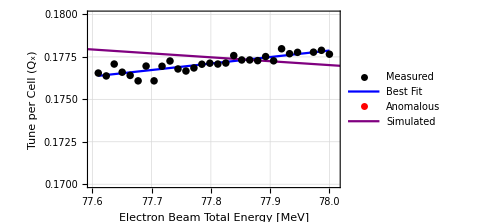

```mathematica
FB78xtune=ListPlot[{FB78measuredx,FB78xbestfitpoints,FB78xdroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.3}],PlotRange->{{77.6,78.01},{0.17,0.18}},ImageSize->Medium]
```

### FB 78 MeV ξ_x Chromaticity

```mathematica
FB78xΔEeEeΔQ=Table[{(FB78xgooddat⟦-1,1⟧-FB78xgooddat⟦i,1⟧)/FB78xgooddat⟦-1,1⟧,FB78xgooddat⟦-1,2⟧-FB78xgooddat⟦i,2⟧},{i,1,(Length[FB78xgooddat⟦All,1⟧]-1)}];
```

```mathematica
FB78xΔEeEeΔQgooddat=Delete[FB78xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FB78xΔEeEeΔQ⟦i,2⟧-Mean[FB78xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB78xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB78xΔEeEeΔQ]}],Null],1]];
```

```mathematica
FB78xpart1chromgood=Fit[FB78xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

-0.000249264

```mathematica
FB78xpart2chromgood=Fit[FB78xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

0.308251

```mathematica
FB78xΔEeEeΔQbestfitpoints=Table[{x,FB78xpart1chromgood+FB78xpart2chromgood*x},{x,Min[FB78xΔEeEeΔQ⟦All,1⟧],Max[FB78xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FB78xΔEeEeΔQdroppedpoints=FB78xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FB78xΔEeEeΔQ⟦i,2⟧-Mean[FB78xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB78xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB78xΔEeEeΔQ]}],Null]⟧
```

{}

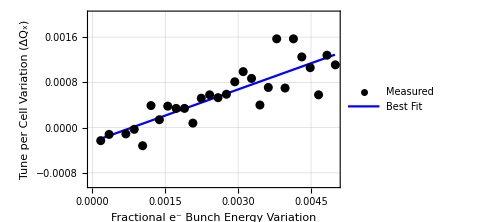

```mathematica
FB78xchromplot=ListPlot[{FB78xΔEeEeΔQgooddat,FB78xΔEeEeΔQbestfitpoints(*,FB78xΔEeEeΔQdroppedpoints*)},Joined->{False,True(*,False*)},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue(*,{Red,PointSize[0.018]}*)},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit"(*,"Anomalous"*)},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.2}],PlotRange->{{0,0.005},{-0.001,0.002}},ImageSize->Medium]
```

### FB 78 MeV ν_y Tune

```mathematica
FB78ygooddat=Delete[FB78measuredy,Partition[DeleteCases[Table[If[Abs[FB78measuredy⟦i,2⟧-Mean[FB78measuredy⟦All,2⟧]]>2*StandardDeviation[FB78measuredy⟦All,2⟧],i],{i,1,Length[FB78measuredy]}],Null],1]];
```

```mathematica
FB78ypart1drop=Fit[FB78ygooddat,{1,x},x]⟦1⟧
```

0.0597404

```mathematica
FB78ypart2drop=Fit[FB78ygooddat,{1,x},x]⟦2,1⟧
```

0.000755313

```mathematica
FB78ydroppedpoints=FB78measuredy⟦DeleteCases[Table[If[Abs[FB78measuredy⟦i,2⟧-Mean[FB78measuredy⟦All,2⟧]]>2*StandardDeviation[FB78measuredy⟦All,2⟧],i],{i,1,Length[FB78measuredy]}],Null]⟧
```

{{77.9597,0.25032}}

```mathematica
FB78ybestfitpoints=Table[{x,FB78ypart1drop+FB78ypart2drop*x},{x,Min[FB78measuredy⟦All,1⟧],Max[FB78measuredy⟦All,1⟧],0.01}];
```

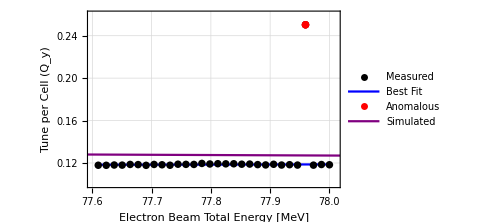

```mathematica
FB78ytune=ListPlot[{FB78measuredy,FB78ybestfitpoints,FB78ydroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{77.6,78.01},{0.1,0.26}},ImageSize->Medium]
```

### FB 78 MeV ξ_y Chromaticity

```mathematica
FB78yΔEeEeΔQ=Table[{(FB78ygooddat⟦-1,1⟧-FB78ygooddat⟦i,1⟧)/FB78ygooddat⟦-1,1⟧,FB78ygooddat⟦-1,2⟧-FB78ygooddat⟦i,2⟧},{i,1,(Length[FB78ygooddat⟦All,1⟧]-1)}];
```

```mathematica
FB78yΔEeEeΔQgooddat=Delete[FB78yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FB78yΔEeEeΔQ⟦i,2⟧-Mean[FB78yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB78yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB78yΔEeEeΔQ]}],Null],1]];
```

```mathematica
FB78ypart1chromgood=Fit[FB78yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

-0.000354414

```mathematica
FB78ypart2chromgood=Fit[FB78yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

0.0768105

```mathematica
FB78yΔEeEeΔQbestfitpoints=Table[{x,FB78ypart1chromgood+FB78ypart2chromgood*x},{x,Min[FB78yΔEeEeΔQ⟦All,1⟧],Max[FB78yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FB78yΔEeEeΔQdroppedpoints=FB78yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FB78yΔEeEeΔQ⟦i,2⟧-Mean[FB78yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB78yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB78yΔEeEeΔQ]}],Null]⟧
```

{{0.00275862,-0.00126}}

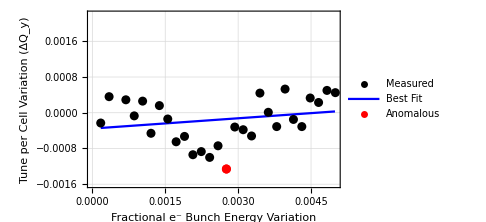

```mathematica
FB78ychromplot=ListPlot[{FB78yΔEeEeΔQgooddat,FB78yΔEeEeΔQbestfitpoints,FB78yΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.78}],PlotRange->{{0,0.005},{-0.0016,0.0022}},ImageSize->Medium]
```

### FB 114 MeV Measured Data

```mathematica
FB114measuredx=Partition[Riffle[Measuredenergies⟦3⟧,tunedata⟦All,43⟧],2];
```

```mathematica
FB114measuredy=Partition[Riffle[Measuredenergies⟦3⟧,tunedata⟦All,47⟧],2];
```

```mathematica
FB114tuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FB114measuredx,FB114measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{113.4,114.01},{0,0.35}},ImageSize->Medium];
```

### FB 114 MeV ν_x Tune

```mathematica
FB114xgooddat=Delete[FB114measuredx,Partition[DeleteCases[Table[If[Abs[FB114measuredx⟦i,2⟧-Mean[FB114measuredx⟦All,2⟧]]>2*StandardDeviation[FB114measuredx⟦All,2⟧],i],{i,1,Length[FB114measuredx]}],Null],1]];
```

```mathematica
FB114xpart1drop=Fit[FB114xgooddat,{1,x},x]⟦1⟧
```

-2.08362

```mathematica
FB114xpart2drop=Fit[FB114xgooddat,{1,x},x]⟦2,1⟧
```

0.0194798

```mathematica
FB114xdroppedpoints=FB114measuredx⟦DeleteCases[Table[If[Abs[FB114measuredx⟦i,2⟧-Mean[FB114measuredx⟦All,2⟧]]>2*StandardDeviation[FB114measuredx⟦All,2⟧],i],{i,1,Length[FB114measuredx]}],Null]⟧
```

{{113.941,0.19376}}

```mathematica
FB114xbestfitpoints=Table[{x,FB114xpart1drop+FB114xpart2drop*x},{x,Min[FB114measuredx⟦All,1⟧],Max[FB114measuredx⟦All,1⟧],0.01}];
```

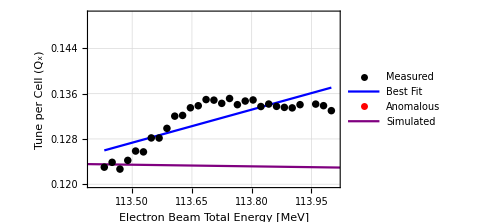

```mathematica
FB114xtune=ListPlot[{FB114measuredx,FB114xbestfitpoints,FB114xdroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],PlotRange->{{113.4,114.01},{0.12,0.15}},ImageSize->Medium]
```

### FB 114 MeV ξ_x Chromaticity

```mathematica
FB114xΔEeEeΔQ=Table[{(FB114xgooddat⟦-1,1⟧-FB114xgooddat⟦i,1⟧)/FB114xgooddat⟦-1,1⟧,FB114xgooddat⟦-1,2⟧-FB114xgooddat⟦i,2⟧},{i,1,(Length[FB114xgooddat⟦All,1⟧]-1)}];
```

```mathematica
FB114xΔEeEeΔQgooddat=Delete[FB114xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FB114xΔEeEeΔQ⟦i,2⟧-Mean[FB114xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB114xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB114xΔEeEeΔQ]}],Null],1]];
```

```mathematica
FB114xpart1chromgood=Fit[FB114xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

-0.00448561

```mathematica
FB114xpart2chromgood=Fit[FB114xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

2.26173

```mathematica
FB114xΔEeEeΔQbestfitpoints=Table[{x,FB114xpart1chromgood+FB114xpart2chromgood*x},{x,Min[FB114xΔEeEeΔQ⟦All,1⟧],Max[FB114xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FB114xΔEeEeΔQdroppedpoints=FB114xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FB114xΔEeEeΔQ⟦i,2⟧-Mean[FB114xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB114xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB114xΔEeEeΔQ]}],Null]⟧
```

{{0.00465517,0.01033}}

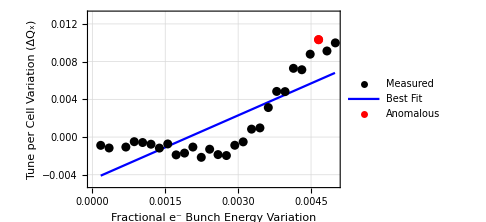

```mathematica
FB114xchromplot=ListPlot[{FB114xΔEeEeΔQgooddat,FB114xΔEeEeΔQbestfitpoints,FB114xΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{0,0.005},{-0.005,0.013}},ImageSize->Medium]
```

### FB 114 MeV ν_y Tune

```mathematica
FB114ygooddat=Delete[FB114measuredy,Partition[DeleteCases[Table[If[Abs[FB114measuredy⟦i,2⟧-Mean[FB114measuredy⟦All,2⟧]]>2*StandardDeviation[FB114measuredy⟦All,2⟧],i],{i,1,Length[FB114measuredy]}],Null],1]];
```

```mathematica
FB114ypart1drop=Fit[FB114ygooddat,{1,x},x]⟦1⟧
```

-0.219073

```mathematica
FB114ypart2drop=Fit[FB114ygooddat,{1,x},x]⟦2,1⟧
```

0.00248894

```mathematica
FB114ydroppedpoints=FB114measuredy⟦DeleteCases[Table[If[Abs[FB114measuredy⟦i,2⟧-Mean[FB114measuredy⟦All,2⟧]]>2*StandardDeviation[FB114measuredy⟦All,2⟧],i],{i,1,Length[FB114measuredy]}],Null]⟧
```

{{113.941,0.10773}}

```mathematica
FB114ybestfitpoints=Table[{x,FB114ypart1drop+FB114ypart2drop*x},{x,Min[FB114measuredy⟦All,1⟧],Max[FB114measuredy⟦All,1⟧],0.01}];
```

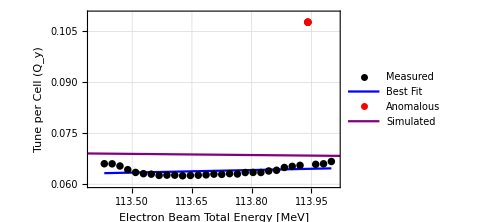

```mathematica
FB114ytune=ListPlot[{FB114measuredy,FB114ybestfitpoints,FB114ydroppedpoints,Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{113.4,114.01},{0.06,0.11}},ImageSize->Medium]
```

### FB 114 MeV ξ_y Chromaticity

```mathematica
FB114yΔEeEeΔQ=Table[{(FB114ygooddat⟦-1,1⟧-FB114ygooddat⟦i,1⟧)/FB114ygooddat⟦-1,1⟧,FB114ygooddat⟦-1,2⟧-FB114ygooddat⟦i,2⟧},{i,1,(Length[FB114ygooddat⟦All,1⟧]-1)}];
```

```mathematica
FB114yΔEeEeΔQgooddat=Delete[FB114yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[FB114yΔEeEeΔQ⟦i,2⟧-Mean[FB114yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB114yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB114yΔEeEeΔQ]}],Null],1]];
```

```mathematica
FB114ypart1chromgood=Fit[FB114yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.00235165

```mathematica
FB114ypart2chromgood=Fit[FB114yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

0.187476

```mathematica
FB114yΔEeEeΔQbestfitpoints=Table[{x,FB114ypart1chromgood+FB114ypart2chromgood*x},{x,Min[FB114yΔEeEeΔQ⟦All,1⟧],Max[FB114yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
FB114yΔEeEeΔQdroppedpoints=FB114yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[FB114yΔEeEeΔQ⟦i,2⟧-Mean[FB114yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[FB114yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[FB114yΔEeEeΔQ]}],Null]⟧
```

{}

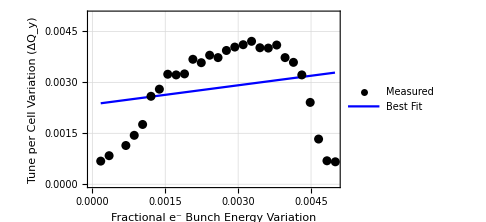

```mathematica
FB114ychromplot=ListPlot[{FB114yΔEeEeΔQgooddat,FB114yΔEeEeΔQbestfitpoints(*,FB114yΔEeEeΔQdroppedpoints*)},Joined->{False,True(*,False*)},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue(*,{Red,PointSize[0.018]}*)},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit"(*,"Anomalous"*)},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.78}],PlotRange->{{0,0.005},{0,0.005}},ImageSize->Medium]
```

### FB 150 MeV Measured Data

```mathematica
FB150measuredx=Partition[Riffle[Measuredenergies⟦4⟧,tunedata⟦All,44⟧],2];
```

```mathematica
FB150measuredy=Partition[Riffle[Measuredenergies⟦4⟧,tunedata⟦All,48⟧],2];
```

```mathematica
FB150tuneplot=ListLinePlot[{Partition[Riffle[arctune⟦1,All⟧,arctune⟦2,All⟧],2],Partition[Riffle[arctune⟦1,All⟧,arctune⟦3,All⟧],2],FB150measuredx,FB150measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.6}],PlotRange->{{148.5,150.01},{0,0.4}},ImageSize->Medium];
```

### FB Group Plots

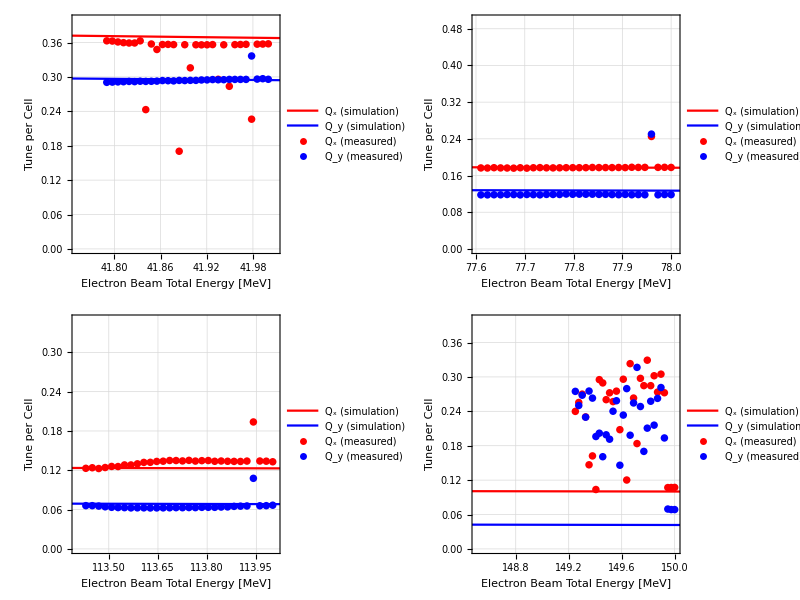

```mathematica
FBtunegrid=Grid[{{FB42tuneplot,FB78tuneplot},{FB114tuneplot,FB150tuneplot}}]
```

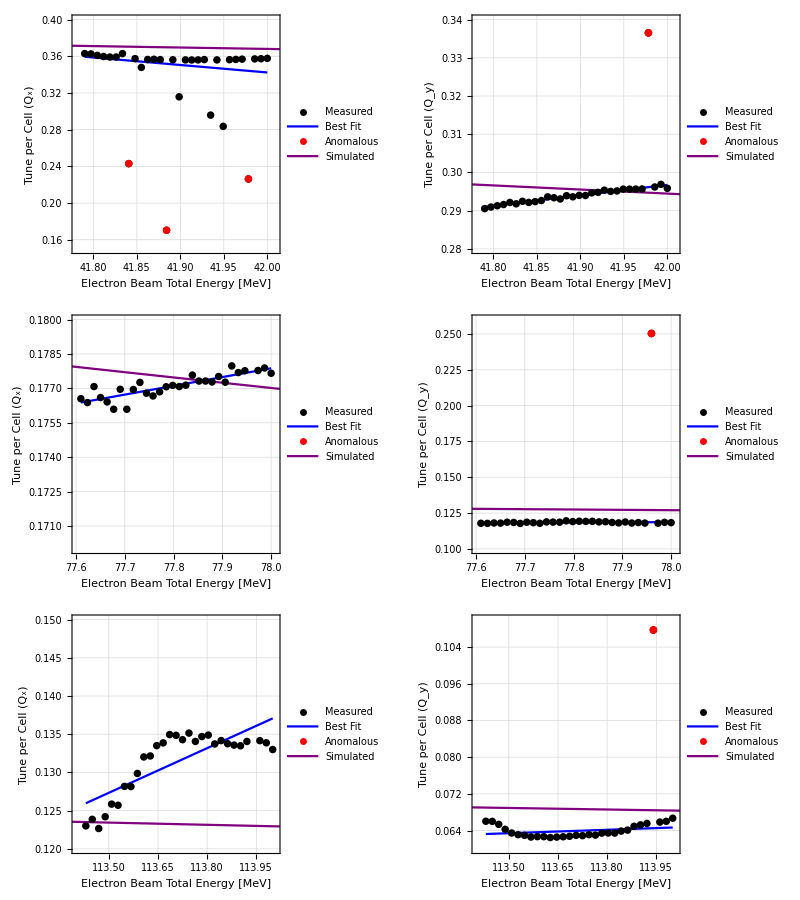

```mathematica
FBtuneanalysedgrid=Grid[{{FB42xtune,FB42ytune},{FB78xtune,FB78ytune},{FB114xtune,FB114ytune}}]
```

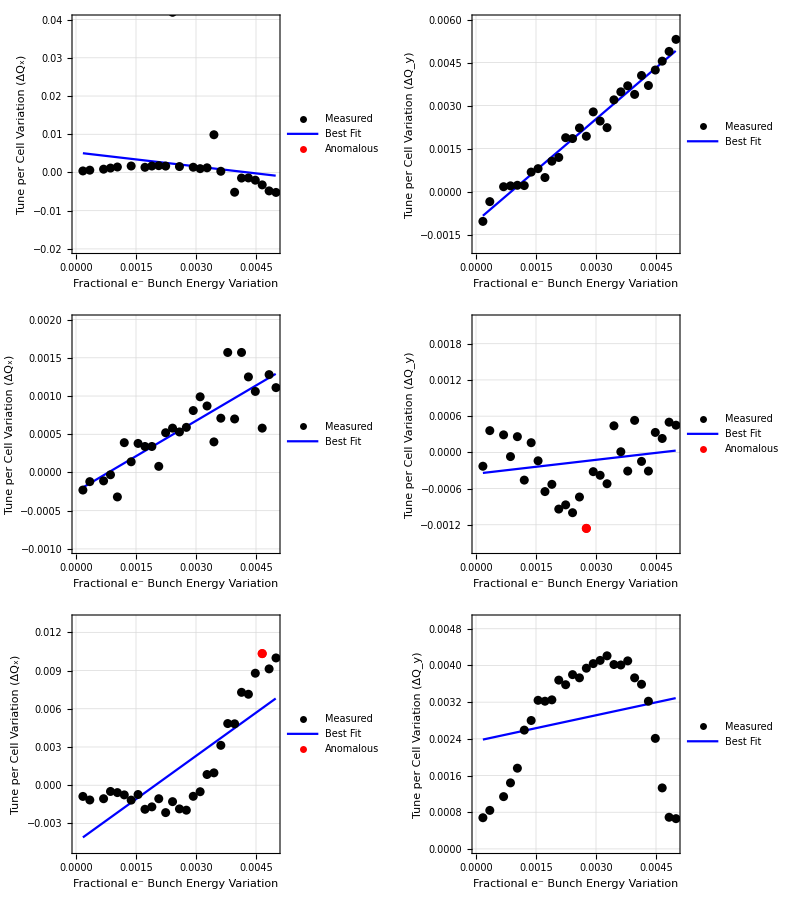

```mathematica
FBchromanalysedgrid=Grid[{{FB42xchromplot,FB42ychromplot},{FB78xchromplot,FB78ychromplot},{FB114xchromplot,FB114ychromplot}}]
```

```mathematica
FBchromtable=Grid[{{"Electron Beam Total Energy [MeV]","FB ξ_x (measured)","FB ξ_y (measured)"},{"42",FB42xpart2chromgood,FB42ypart2chromgood},{"78",FB78xpart2chromgood,FB78ypart2chromgood},{"114",FB114xpart2chromgood,FB114ypart2chromgood}},Dividers->All]
```

Electron Beam Total Energy [MeV] | FB ξ_x (measured) | FB ξ_y (measured)
42 | -1.21876 | 1.19302
78 | 0.308251 | 0.0768105
114 | 2.26173 | 0.187476

```mathematica
FBchromvals={Nominalenergies⟦1;;3⟧,{FB42xpart2chromgood,FB78xpart2chromgood,FB114xpart2chromgood},{FB42ypart2chromgood,FB78ypart2chromgood,FB114ypart2chromgood}};
```

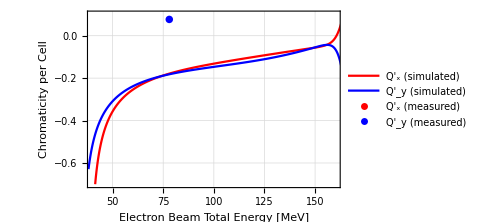

```mathematica
FBchrommeasured=ListPlot[{Partition[Riffle[Drop[arctune⟦1,All⟧,1],arcchrom⟦All,1⟧],2],Partition[Riffle[Drop[arctune⟦1,All⟧,1],arcchrom⟦All,2⟧],2],Partition[Riffle[FBchromvals⟦1,All⟧,FBchromvals⟦2,All⟧],2],Partition[Riffle[FBchromvals⟦1,All⟧,FBchromvals⟦3,All⟧],2]},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Chromaticity per Cell"},PlotLegends->Placed[LineLegend[{"Q'_x (simulated)","Q'_y (simulated)","Q'_x (measured)","Q'_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.3}],PlotRange->{{40,160},{-0.7,0.1}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\Tune_Plots"];
Export["FB_analysed_3turn_tunes.pdf",FBtuneanalysedgrid];
Export["FB_analysed_3turn_dEedQ.pdf",FAchromanalysedgrid];
Export["FB_analysed_chromaticity.pdf",FAchrommeasured];
```

## ZX

### ZX 42 MeV Measured Data

```mathematica
ZX42measuredx=Partition[Riffle[Measuredenergies⟦1⟧,tunedata⟦All,25⟧],2];
```

```mathematica
ZX42measuredy=Partition[Riffle[Measuredenergies⟦1⟧,tunedata⟦All,29⟧],2];
```

```mathematica
ZX42tuneplot=ListLinePlot[{Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2],Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2],ZX42measuredx,ZX42measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.77,0.3}],PlotRange->{{41.75,42.01},{0,0.4}},ImageSize->Medium];
```

### ZX 42 MeV ν_x Tune

```mathematica
ZX42xgooddat=Delete[ZX42measuredx,Partition[DeleteCases[Table[If[Abs[ZX42measuredx⟦i,2⟧-Mean[ZX42measuredx⟦All,2⟧]]>2*StandardDeviation[ZX42measuredx⟦All,2⟧],i],{i,1,Length[ZX42measuredx]}],Null],1]];
```

```mathematica
ZX42xpart1drop=Fit[ZX42xgooddat,{1,x},x]⟦1⟧
```

3.96263

```mathematica
ZX42xpart2drop=Fit[ZX42xgooddat,{1,x},x]⟦2,1⟧
```

-0.085932

```mathematica
ZX42xdroppedpoints=ZX42measuredx⟦DeleteCases[Table[If[Abs[ZX42measuredx⟦i,2⟧-Mean[ZX42measuredx⟦All,2⟧]]>2*StandardDeviation[ZX42measuredx⟦All,2⟧],i],{i,1,Length[ZX42measuredx]}],Null]⟧
```

{{41.8407,0.21882},{41.8841,0.22609}}

```mathematica
ZX42xbestfitpoints=Table[{x,ZX42xpart1drop+ZX42xpart2drop*x},{x,Min[ZX42measuredx⟦All,1⟧],Max[ZX42measuredx⟦All,1⟧],0.01}];
```

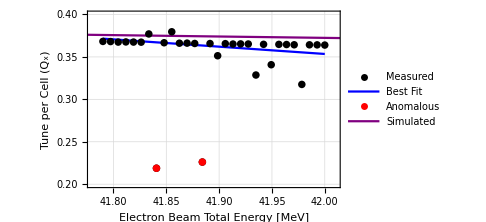

```mathematica
ZX42xtune=ListPlot[{ZX42measuredx,ZX42xbestfitpoints,ZX42xdroppedpoints,Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.45}],PlotRange->{{41.78,42.01},{0.2,0.4}},ImageSize->Medium]
```

### ZX 42 MeV ξ_x Chromaticity

```mathematica
ZX42xΔEeEeΔQ=Table[{(ZX42xgooddat⟦-1,1⟧-ZX42xgooddat⟦i,1⟧)/ZX42xgooddat⟦-1,1⟧,ZX42xgooddat⟦-1,2⟧-ZX42xgooddat⟦i,2⟧},{i,1,(Length[ZX42xgooddat⟦All,1⟧]-1)}];
```

```mathematica
ZX42xΔEeEeΔQgooddat=Delete[ZX42xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[ZX42xΔEeEeΔQ⟦i,2⟧-Mean[ZX42xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX42xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX42xΔEeEeΔQ]}],Null],1]];
```

```mathematica
ZX42xpart1chromgood=Fit[ZX42xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.00387768

```mathematica
ZX42xpart2chromgood=Fit[ZX42xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-1.98981

```mathematica
ZX42xΔEeEeΔQbestfitpoints=Table[{x,ZX42xpart1chromgood+ZX42xpart2chromgood*x},{x,Min[ZX42xΔEeEeΔQ⟦All,1⟧],Max[ZX42xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
ZX42xΔEeEeΔQdroppedpoints=ZX42xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[ZX42xΔEeEeΔQ⟦i,2⟧-Mean[ZX42xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX42xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX42xΔEeEeΔQ]}],Null]⟧;
```

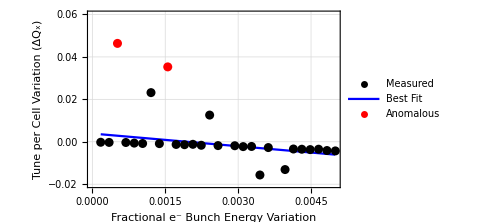

```mathematica
ZX42xchromplot=ListPlot[{ZX42xΔEeEeΔQgooddat,ZX42xΔEeEeΔQbestfitpoints,ZX42xΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.78}],PlotRange->{{0,0.005},{-0.02,0.06}},ImageSize->Medium]
```

### ZX 42 MeV ν_y Tune

```mathematica
ZX42ygooddat=Delete[ZX42measuredy,Partition[DeleteCases[Table[If[Abs[ZX42measuredy⟦i,2⟧-Mean[ZX42measuredy⟦All,2⟧]]>2*StandardDeviation[ZX42measuredy⟦All,2⟧],i],{i,1,Length[ZX42measuredy]}],Null],1]];
```

```mathematica
ZX42ypart1drop=Fit[ZX42ygooddat,{1,x},x]⟦1⟧
```

0.499294

```mathematica
ZX42ypart2drop=Fit[ZX42ygooddat,{1,x},x]⟦2,1⟧
```

-0.0051467

```mathematica
ZX42ydroppedpoints=ZX42measuredy⟦DeleteCases[Table[If[Abs[ZX42measuredy⟦i,2⟧-Mean[ZX42measuredy⟦All,2⟧]]>2*StandardDeviation[ZX42measuredy⟦All,2⟧],i],{i,1,Length[ZX42measuredy]}],Null]⟧
```

{{41.9783,0.29483}}

```mathematica
ZX42ybestfitpoints=Table[{x,ZX42ypart1drop+ZX42ypart2drop*x},{x,Min[ZX42measuredy⟦All,1⟧],Max[ZX42measuredy⟦All,1⟧],0.01}];
```

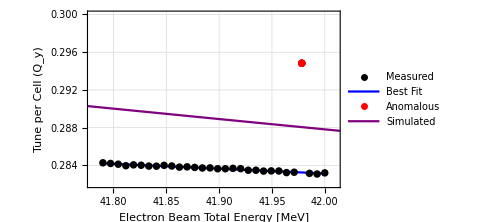

```mathematica
ZX42ytune=ListPlot[{ZX42measuredy,ZX42ybestfitpoints,ZX42ydroppedpoints,Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{41.78,42.01},{0.282,0.3}},ImageSize->Medium]
```

### ZX 42 MeV ξ_y Chromaticity

```mathematica
ZX42yΔEeEeΔQ=Table[{(ZX42ygooddat⟦-1,1⟧-ZX42ygooddat⟦i,1⟧)/ZX42ygooddat⟦-1,1⟧,ZX42ygooddat⟦-1,2⟧-ZX42ygooddat⟦i,2⟧},{i,1,(Length[ZX42ygooddat⟦All,1⟧]-1)}];
```

```mathematica
ZX42yΔEeEeΔQgooddat=Delete[ZX42yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[ZX42yΔEeEeΔQ⟦i,2⟧-Mean[ZX42yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX42yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX42yΔEeEeΔQ]}],Null],1]];
```

```mathematica
ZX42ypart1chromgood=Fit[ZX42yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.0000781654

```mathematica
ZX42ypart2chromgood=Fit[ZX42yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.219361

```mathematica
ZX42yΔEeEeΔQbestfitpoints=Table[{x,ZX42ypart1chromgood+ZX42ypart2chromgood*x},{x,Min[ZX42yΔEeEeΔQ⟦All,1⟧],Max[ZX42yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
ZX42yΔEeEeΔQdroppedpoints=ZX42yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[ZX42yΔEeEeΔQ⟦i,2⟧-Mean[ZX42yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX42yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX42yΔEeEeΔQ]}],Null]⟧;
```

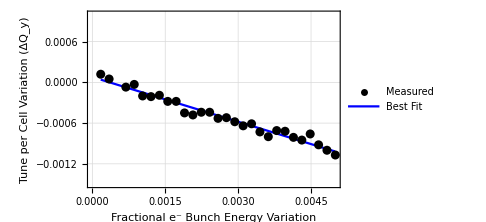

```mathematica
ZX42ychromplot=ListPlot[{ZX42yΔEeEeΔQgooddat,ZX42yΔEeEeΔQbestfitpoints(*,ZX42yΔEeEeΔQdroppedpoints*)},Joined->{False,True(*,False*)},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue(*,{Red,PointSize[0.018]}*)},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit"(*,"Anomalous"*)},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.78}],PlotRange->{{0,0.005},{-0.0015,0.001}},ImageSize->Medium]
```

### ZX 78 MeV Measured Data

```mathematica
ZX78measuredx=Partition[Riffle[Measuredenergies⟦2⟧,tunedata⟦All,26⟧],2];
```

```mathematica
ZX78measuredy=Partition[Riffle[Measuredenergies⟦2⟧,tunedata⟦All,30⟧],2];
```

```mathematica
ZX78tuneplot=ListLinePlot[{Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2],Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2],ZX78measuredx,ZX78measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.7}],PlotRange->{{77.6,78.01},{0,0.5}},ImageSize->Medium];
```

### ZX 78 MeV ν_x Tune

```mathematica
ZX78xgooddat=Delete[ZX78measuredx,Partition[DeleteCases[Table[If[Abs[ZX78measuredx⟦i,2⟧-Mean[ZX78measuredx⟦All,2⟧]]>2*StandardDeviation[ZX78measuredx⟦All,2⟧],i],{i,1,Length[ZX78measuredx]}],Null],1]];
```

```mathematica
ZX78xpart1drop=Fit[ZX78xgooddat,{1,x},x]⟦1⟧
```

0.457883

```mathematica
ZX78xpart2drop=Fit[ZX78xgooddat,{1,x},x]⟦2,1⟧
```

-0.0035805

```mathematica
ZX78xdroppedpoints=ZX78measuredx⟦DeleteCases[Table[If[Abs[ZX78measuredx⟦i,2⟧-Mean[ZX78measuredx⟦All,2⟧]]>2*StandardDeviation[ZX78measuredx⟦All,2⟧],i],{i,1,Length[ZX78measuredx]}],Null]⟧
```

{{77.9597,0.36938}}

```mathematica
ZX78xbestfitpoints=Table[{x,ZX78xpart1drop+ZX78xpart2drop*x},{x,Min[ZX78measuredx⟦All,1⟧],Max[ZX78measuredx⟦All,1⟧],0.01}];
```

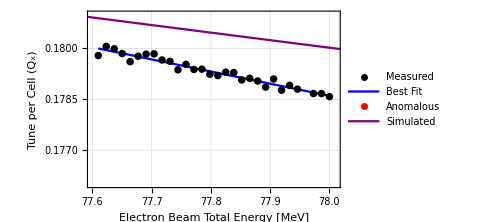

```mathematica
ZX78xtune=ListPlot[{ZX78measuredx,ZX78xbestfitpoints,ZX78xdroppedpoints,Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.3}],PlotRange->{{77.6,78.01},{0.176,0.181}},ImageSize->Medium]
```

### ZX 78 MeV ξ_x Chromaticity

```mathematica
ZX78xΔEeEeΔQ=Table[{(ZX78xgooddat⟦-1,1⟧-ZX78xgooddat⟦i,1⟧)/ZX78xgooddat⟦-1,1⟧,ZX78xgooddat⟦-1,2⟧-ZX78xgooddat⟦i,2⟧},{i,1,(Length[ZX78xgooddat⟦All,1⟧]-1)}];
```

```mathematica
ZX78xΔEeEeΔQgooddat=Delete[ZX78xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[ZX78xΔEeEeΔQ⟦i,2⟧-Mean[ZX78xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX78xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX78xΔEeEeΔQ]}],Null],1]];
```

```mathematica
ZX78xpart1chromgood=Fit[ZX78xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

-0.0000275942

```mathematica
ZX78xpart2chromgood=Fit[ZX78xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.27815

```mathematica
ZX78xΔEeEeΔQbestfitpoints=Table[{x,ZX78xpart1chromgood+ZX78xpart2chromgood*x},{x,Min[ZX78xΔEeEeΔQ⟦All,1⟧],Max[ZX78xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
ZX78xΔEeEeΔQdroppedpoints=ZX78xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[ZX78xΔEeEeΔQ⟦i,2⟧-Mean[ZX78xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX78xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX78xΔEeEeΔQ]}],Null]⟧;
```

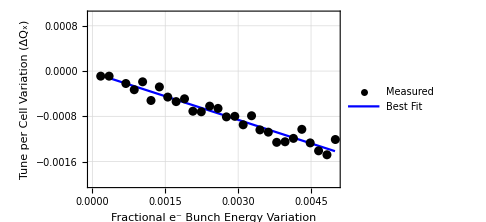

```mathematica
ZX78xchromplot=ListPlot[{ZX78xΔEeEeΔQgooddat,ZX78xΔEeEeΔQbestfitpoints(*,ZX78xΔEeEeΔQdroppedpoints*)},Joined->{False,True(*,False*)},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue(*,{Red,PointSize[0.018]}*)},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit"(*,"Anomalous"*)},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.82}],PlotRange->{{0,0.005},{-0.002,0.001}},ImageSize->Medium]
```

### ZX 78 MeV ν_y Tune

```mathematica
ZX78ygooddat=Delete[ZX78measuredy,Partition[DeleteCases[Table[If[Abs[ZX78measuredy⟦i,2⟧-Mean[ZX78measuredy⟦All,2⟧]]>2*StandardDeviation[ZX78measuredy⟦All,2⟧],i],{i,1,Length[ZX78measuredy]}],Null],1]];
```

```mathematica
ZX78ypart1drop=Fit[ZX78ygooddat,{1,x},x]⟦1⟧
```

0.225368

```mathematica
ZX78ypart2drop=Fit[ZX78ygooddat,{1,x},x]⟦2,1⟧
```

-0.00138628

```mathematica
ZX78ydroppedpoints=ZX78measuredy⟦DeleteCases[Table[If[Abs[ZX78measuredy⟦i,2⟧-Mean[ZX78measuredy⟦All,2⟧]]>2*StandardDeviation[ZX78measuredy⟦All,2⟧],i],{i,1,Length[ZX78measuredy]}],Null]⟧
```

{{77.9597,0.23913}}

```mathematica
ZX78ybestfitpoints=Table[{x,ZX78ypart1drop+ZX78ypart2drop*x},{x,Min[ZX78measuredy⟦All,1⟧],Max[ZX78measuredy⟦All,1⟧],0.01}];
```

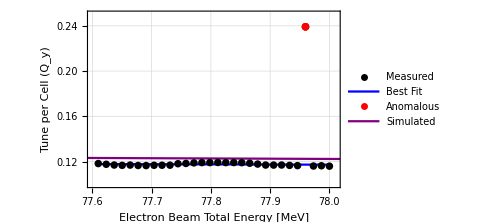

```mathematica
ZX78ytune=ListPlot[{ZX78measuredy,ZX78ybestfitpoints,ZX78ydroppedpoints,Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{77.6,78.01},{0.10,0.25}},ImageSize->Medium]
```

### ZX 78 MeV ξ_y Chromaticity

```mathematica
ZX78yΔEeEeΔQ=Table[{(ZX78ygooddat⟦-1,1⟧-ZX78ygooddat⟦i,1⟧)/ZX78ygooddat⟦-1,1⟧,ZX78ygooddat⟦-1,2⟧-ZX78ygooddat⟦i,2⟧},{i,1,(Length[ZX78ygooddat⟦All,1⟧]-1)}];
```

```mathematica
ZX78yΔEeEeΔQgooddat=Delete[ZX78yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[ZX78yΔEeEeΔQ⟦i,2⟧-Mean[ZX78yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX78yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX78yΔEeEeΔQ]}],Null],1]];
```

```mathematica
ZX78ypart1chromgood=Fit[ZX78yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

-0.00149798

```mathematica
ZX78ypart2chromgood=Fit[ZX78yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.0468106

```mathematica
ZX78yΔEeEeΔQbestfitpoints=Table[{x,ZX78ypart1chromgood+ZX78ypart2chromgood*x},{x,Min[ZX78yΔEeEeΔQ⟦All,1⟧],Max[ZX78yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
ZX78yΔEeEeΔQdroppedpoints=ZX78yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[ZX78yΔEeEeΔQ⟦i,2⟧-Mean[ZX78yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX78yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX78yΔEeEeΔQ]}],Null]⟧
```

{}

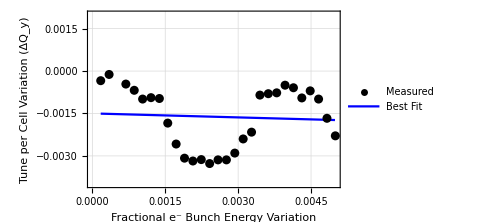

```mathematica
ZX78ychromplot=ListPlot[{ZX78yΔEeEeΔQgooddat,ZX78yΔEeEeΔQbestfitpoints(*,ZX78yΔEeEeΔQdroppedpoints*)},Joined->{False,True(*,False*)},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue(*,{Red,PointSize[0.018]}*)},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit"(*,"Anomalous"*)},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.8}],PlotRange->{{0,0.005},{-0.004,0.002}},ImageSize->Medium]
```

### ZX 114 Measured Data

```mathematica
ZX114measuredx=Partition[Riffle[Measuredenergies⟦3⟧,tunedata⟦All,27⟧],2];
```

```mathematica
ZX114measuredy=Partition[Riffle[Measuredenergies⟦3⟧,tunedata⟦All,31⟧],2];
```

```mathematica
ZX114tuneplot=ListLinePlot[{Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2],Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2],ZX114measuredx,ZX114measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{113.4,114.01},{0,0.35}},ImageSize->Medium];
```

### ZX 114 MeV ν_x Tune

```mathematica
ZX114xgooddat=Delete[ZX114measuredx,Partition[DeleteCases[Table[If[Abs[ZX114measuredx⟦i,2⟧-Mean[ZX114measuredx⟦All,2⟧]]>2*StandardDeviation[ZX114measuredx⟦All,2⟧],i],{i,1,Length[ZX114measuredx]}],Null],1]];
```

```mathematica
ZX114xpart1drop=Fit[ZX114xgooddat,{1,x},x]⟦1⟧
```

0.49715

```mathematica
ZX114xpart2drop=Fit[ZX114xgooddat,{1,x},x]⟦2,1⟧
```

-0.0032829

```mathematica
ZX114xdroppedpoints=ZX114measuredx⟦DeleteCases[Table[If[Abs[ZX114measuredx⟦i,2⟧-Mean[ZX114measuredx⟦All,2⟧]]>2*StandardDeviation[ZX114measuredx⟦All,2⟧],i],{i,1,Length[ZX114measuredx]}],Null]⟧
```

{{113.941,0.29881}}

```mathematica
ZX114xbestfitpoints=Table[{x,ZX114xpart1drop+ZX114xpart2drop*x},{x,Min[ZX114measuredx⟦All,1⟧],Max[ZX114measuredx⟦All,1⟧],0.01}];
```

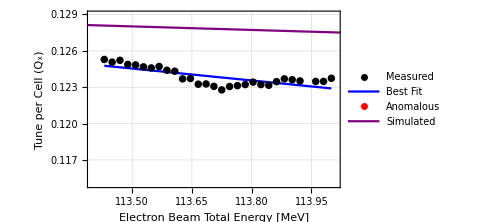

```mathematica
ZX114xtune=ListPlot[{ZX114measuredx,ZX114xbestfitpoints,ZX114xdroppedpoints,Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.3}],PlotRange->{{113.4,114.01},{0.115,0.129}},ImageSize->Medium]
```

### ZX 114 MeV ξ_x Chromaticity

```mathematica
ZX114xΔEeEeΔQ=Table[{(ZX114xgooddat⟦-1,1⟧-ZX114xgooddat⟦i,1⟧)/ZX114xgooddat⟦-1,1⟧,ZX114xgooddat⟦-1,2⟧-ZX114xgooddat⟦i,2⟧},{i,1,(Length[ZX114xgooddat⟦All,1⟧]-1)}];
```

```mathematica
ZX114xΔEeEeΔQgooddat=Delete[ZX114xΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[ZX114xΔEeEeΔQ⟦i,2⟧-Mean[ZX114xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX114xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX114xΔEeEeΔQ]}],Null],1]];
```

```mathematica
ZX114xpart1chromgood=Fit[ZX114xΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.000976117

```mathematica
ZX114xpart2chromgood=Fit[ZX114xΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.414207

```mathematica
ZX114xΔEeEeΔQbestfitpoints=Table[{x,ZX114xpart1chromgood+ZX114xpart2chromgood*x},{x,Min[ZX114xΔEeEeΔQ⟦All,1⟧],Max[ZX114xΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
ZX114xΔEeEeΔQdroppedpoints=ZX114xΔEeEeΔQ⟦DeleteCases[Table[If[Abs[ZX114xΔEeEeΔQ⟦i,2⟧-Mean[ZX114xΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX114xΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX114xΔEeEeΔQ]}],Null]⟧
```

{}

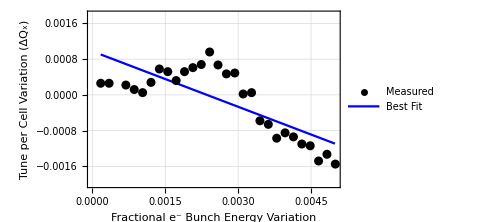

```mathematica
ZX114xchromplot=ListPlot[{ZX114xΔEeEeΔQgooddat,ZX114xΔEeEeΔQbestfitpoints(*,ZX114xΔEeEeΔQdroppedpoints*)},Joined->{False,True(*,False*)},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue(*,{Red,PointSize[0.018]}*)},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_x)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit"(*,"Anomalous"*)},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.82}],PlotRange->{{0,0.005},{-0.002,0.0018}},ImageSize->Medium]
```

### ZX 114 MeV ν_y Tune

```mathematica
ZX114ygooddat=Delete[ZX114measuredy,Partition[DeleteCases[Table[If[Abs[ZX114measuredy⟦i,2⟧-Mean[ZX114measuredy⟦All,2⟧]]>2*StandardDeviation[ZX114measuredy⟦All,2⟧],i],{i,1,Length[ZX114measuredy]}],Null],1]];
```

```mathematica
ZX114ypart1drop=Fit[ZX114ygooddat,{1,x},x]⟦1⟧
```

0.242868

```mathematica
ZX114ypart2drop=Fit[ZX114ygooddat,{1,x},x]⟦2,1⟧
```

-0.00150189

```mathematica
ZX114ydroppedpoints=ZX114measuredy⟦DeleteCases[Table[If[Abs[ZX114measuredy⟦i,2⟧-Mean[ZX114measuredy⟦All,2⟧]]>2*StandardDeviation[ZX114measuredy⟦All,2⟧],i],{i,1,Length[ZX114measuredy]}],Null]⟧
```

{{113.941,0.10531}}

```mathematica
ZX114ybestfitpoints=Table[{x,ZX114ypart1drop+ZX114ypart2drop*x},{x,Min[ZX114measuredy⟦All,1⟧],Max[ZX114measuredy⟦All,1⟧],0.01}];
```

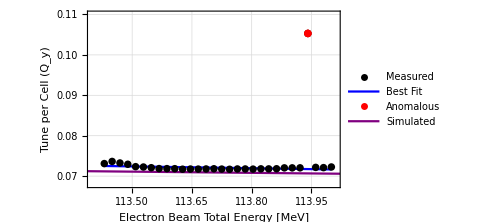

```mathematica
ZX114ytune=ListPlot[{ZX114measuredy,ZX114ybestfitpoints,ZX114ydroppedpoints,Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2]},Joined->{False,True,False,True},PlotStyle->{{Black,PointSize[0.015]},Blue,{Red,PointSize[0.015]},Purple},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell (Q_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous","Simulated"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],PlotRange->{{113.4,114.01},{0.068,0.11}},ImageSize->Medium]
```

### ZX 114 MeV ξ_y Chromaticity

```mathematica
ZX114yΔEeEeΔQ=Table[{(ZX114ygooddat⟦-1,1⟧-ZX114ygooddat⟦i,1⟧)/ZX114ygooddat⟦-1,1⟧,ZX114ygooddat⟦-1,2⟧-ZX114ygooddat⟦i,2⟧},{i,1,(Length[ZX114ygooddat⟦All,1⟧]-1)}];
```

```mathematica
ZX114yΔEeEeΔQgooddat=Delete[ZX114yΔEeEeΔQ,Partition[DeleteCases[Table[If[Abs[ZX114yΔEeEeΔQ⟦i,2⟧-Mean[ZX114yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX114yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX114yΔEeEeΔQ]}],Null],1]];
```

```mathematica
ZX114ypart1chromgood=Fit[ZX114yΔEeEeΔQgooddat,{1,x},x]⟦1⟧
```

0.000550846

```mathematica
ZX114ypart2chromgood=Fit[ZX114yΔEeEeΔQgooddat,{1,x},x]⟦2,1⟧
```

-0.109261

```mathematica
ZX114yΔEeEeΔQbestfitpoints=Table[{x,ZX114ypart1chromgood+ZX114ypart2chromgood*x},{x,Min[ZX114yΔEeEeΔQ⟦All,1⟧],Max[ZX114yΔEeEeΔQ⟦All,1⟧],0.00001}];
```

```mathematica
ZX114yΔEeEeΔQdroppedpoints=ZX114yΔEeEeΔQ⟦DeleteCases[Table[If[Abs[ZX114yΔEeEeΔQ⟦i,2⟧-Mean[ZX114yΔEeEeΔQ⟦All,2⟧]]>2*StandardDeviation[ZX114yΔEeEeΔQ⟦All,2⟧],i],{i,1,Length[ZX114yΔEeEeΔQ]}],Null]⟧
```

{{0.00482759,-0.00137},{0.00465517,-0.00099}}

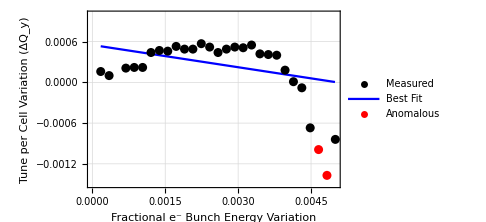

```mathematica
ZX114ychromplot=ListPlot[{ZX114yΔEeEeΔQgooddat,ZX114yΔEeEeΔQbestfitpoints,ZX114yΔEeEeΔQdroppedpoints},Joined->{False,True,False},Frame->True,PlotStyle->{{Black,PointSize[0.018]},Blue,{Red,PointSize[0.018]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Fractional e^- Bunch Energy Variation","Tune per Cell Variation (ΔQ_y)"},PlotLegends->Placed[LineLegend[{"Measured","Best Fit","Anomalous"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.3}],PlotRange->{{0,0.005},{-0.0015,0.001}},ImageSize->Medium]
```

### ZX 150 Measured Data

```mathematica
ZX150measuredx=Partition[Riffle[Measuredenergies⟦4⟧,tunedata⟦All,28⟧],2];
```

```mathematica
ZX150measuredy=Partition[Riffle[Measuredenergies⟦4⟧,tunedata⟦All,32⟧],2];
```

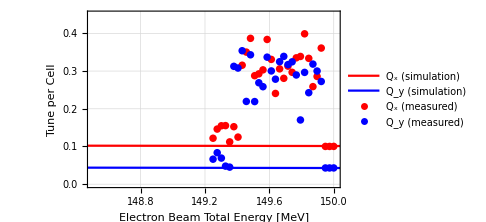

```mathematica
ZX150tuneplot=ListLinePlot[{Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦2,All⟧],2],Partition[Riffle[straighttune⟦1,All⟧,straighttune⟦3,All⟧],2],ZX150measuredx,ZX150measuredy},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Tune per Cell"},(*PlotLabel->"CBETA FFA FA/FB Fieldmap Tune",*)PlotLegends->Placed[LineLegend[{"Q_x (simulation)","Q_y (simulation)","Q_x (measured)","Q_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.6}],PlotRange->{{148.5,150.01},{0,0.45}},ImageSize->Medium]
```

### ZX Group Plots

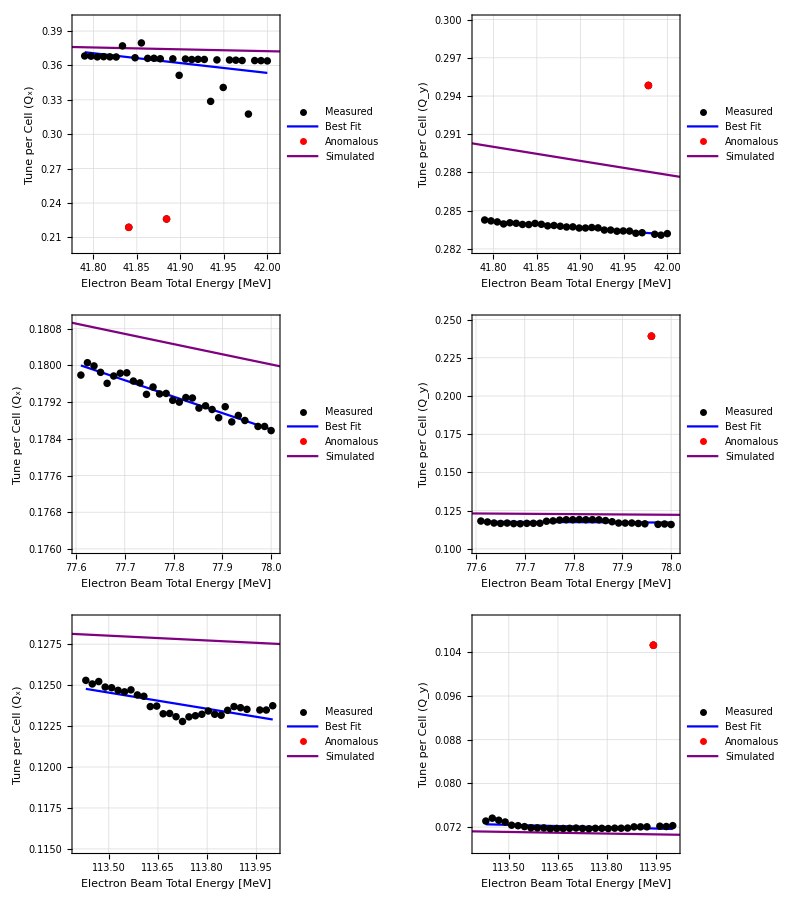

```mathematica
ZXtuneanalysedgrid=Grid[{{ZX42xtune,ZX42ytune},{ZX78xtune,ZX78ytune},{ZX114xtune,ZX114ytune}}]
```

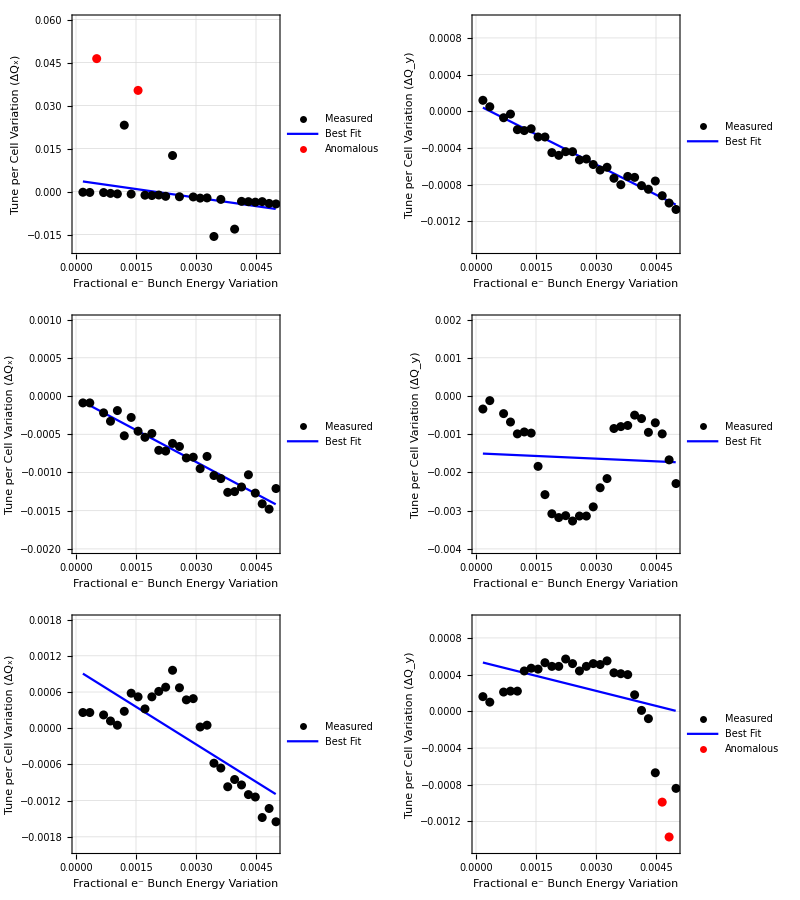

```mathematica
ZXchromanalysedgrid=Grid[{{ZX42xchromplot,ZX42ychromplot},{ZX78xchromplot,ZX78ychromplot},{ZX114xchromplot,ZX114ychromplot}}]
```

```mathematica
ZXchromtable=Grid[{{"Electron Beam Total Energy [MeV]","ZX ξ_x (measured)","ZX ξ_y (measured)"},{"42",ZX42xpart2chromgood,ZX42ypart2chromgood},{"78",ZX78xpart2chromgood,ZX78ypart2chromgood},{"114",ZX114xpart2chromgood,ZX114ypart2chromgood}},Dividers->All]
```

Electron Beam Total Energy [MeV] | ZX ξ_x (measured) | ZX ξ_y (measured)
42 | -1.98981 | -0.219361
78 | -0.27815 | -0.0468106
114 | -0.414207 | -0.109261

```mathematica
ZXchromvals={Nominalenergies⟦1;;3⟧,{ZX42xpart2chromgood,ZX78xpart2chromgood,ZX114xpart2chromgood},{ZX42ypart2chromgood,ZX78ypart2chromgood,ZX114ypart2chromgood}};
```

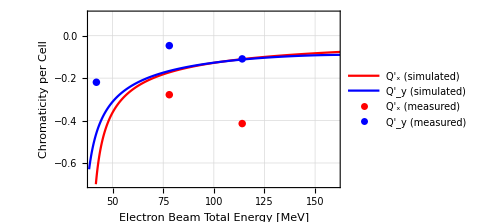

```mathematica
ZXchrommeasured=ListPlot[{Partition[Riffle[Drop[straighttune⟦1,All⟧,1],straightchrom⟦All,1⟧],2],Partition[Riffle[Drop[straighttune⟦1,All⟧,1],straightchrom⟦All,2⟧],2],Partition[Riffle[ZXchromvals⟦1,All⟧,ZXchromvals⟦2,All⟧],2],Partition[Riffle[ZXchromvals⟦1,All⟧,ZXchromvals⟦3,All⟧],2]},Joined->{True,True,False,False},Frame->True,PlotStyle->{Red,Blue,{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},GridLines->Automatic,FrameLabel->{"Electron Beam Total Energy [MeV]","Chromaticity per Cell"},PlotLegends->Placed[LineLegend[{"Q'_x (simulated)","Q'_y (simulated)","Q'_x (measured)","Q'_y (measured)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.3}],PlotRange->{{40,160},{-0.7,0.1}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\Tune_Plots"];
Export["ZX_analysed_3turn_tunes.pdf",ZXtuneanalysedgrid];
Export["ZX_analysed_3turn_dEedQ.pdf",ZXchromanalysedgrid];
Export["ZX_analysed_chromaticity.pdf",ZXchrommeasured];
```

## Bad 150 MeV Plots

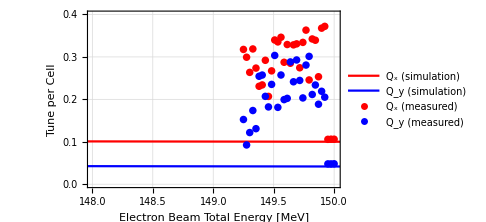
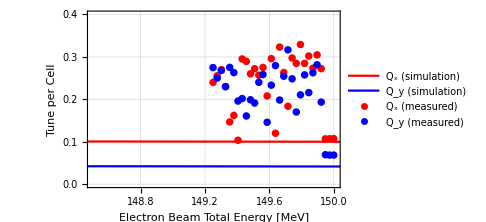
-Graphics- | -Graphics-
-Graphics- |

```mathematica
FAFBZXtune150=Grid[{{FA150tuneplot,FB150tuneplot},{ZX150tuneplot}}]
```

```mathematica
SetDirectory["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\Tune_Plots"];
Export["FAFBZX_150_tunes.pdf",FAFBZXtune150];
```

## Chromaticity Plots

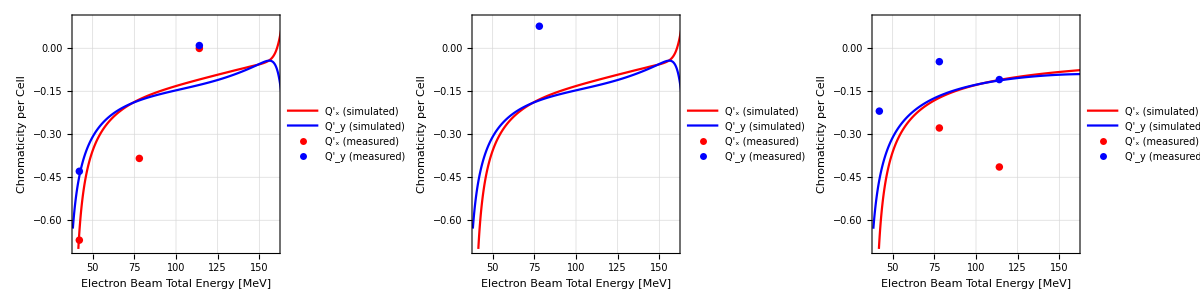

```mathematica
FINchromgrid=Grid[{{FAchrommeasured,FBchrommeasured,ZXchrommeasured}}]
```

```mathematica
SetDirectory["C:\Users\user\Documents\Wolfram Mathematica\CBETAchromaticity\Tune_Plots"];
Export["FAFBZX_chromaticity.pdf",FINchromgrid];
```